```mathematica
SetDirectory[NotebookDirectory[]];<<ABCInterpolator.m
```

```mathematica
X1=Collect[n^(-p)Integrate[(t^(5/2)/n^5 - t^(15/2))t^(-p)(A + B t κ) E^(-C t κ),{t,0,Infinity}, GenerateConditions->False],n]
```

n^(-5-p) κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p])+n^-p κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p])

```mathematica
(n^(-5-p) κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p])+n^-p κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p]))//.n^(x_):> Zeta[-x-1]/Zeta[-x]
```

(κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p]) Zeta[-1+p])/Zeta[p]+(κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p]) Zeta[4+p])/Zeta[5+p]

```mathematica
I1 =FullSimplify[((κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p]) Zeta[-1+p])/(p Zeta[p]))/.{p->17/2 + q,κ->1 }]
```

(2 C^(-1+q) (-A C+B q) Gamma[-q] Zeta[15/2+q])/((17+2 q) Zeta[17/2+q])

```mathematica
I2 =FullSimplify[((κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p]) Zeta[4+p])/(p Zeta[5+p]))/.{p->19/2 -6+ q,κ->1 }]
```

(2 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((7+2 q) Zeta[17/2+q])

```mathematica
I1 + I2//FullSimplify
```

(20 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q])

```mathematica
Factor[(119+48 q+4 q^2)]
```

(7+2 q) (17+2 q)

```mathematica
((Gamma[-q] Zeta[15/2+q])/((7+2 q) (17+2 q) Zeta[17/2+q]))/.q->p
```

(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p])

```mathematica
F == 20 C^(-1+q) (A C-B q)
```

F==20 C^(-1+q) (A C-B q)

```mathematica
pts = FunctionPoles[{(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]),{ Abs[p] < 50}},p]
```

{{-97/2,1},{-93/2,1},{-89/2,1},{-85/2,1},{-81/2,1},{-77/2,1},{-73/2,1},{-69/2,1},{-65/2,1},{-61/2,1},{-57/2,1},{-53/2,1},{-49/2,1},{-45/2,1},{-41/2,1},{-37/2,1},{-33/2,1},{-29/2,1},{-25/2,1},{-21/2,1},{-17/2,1},{-13/2,1},{-7/2,1},{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,1},{24,1},{25,1},{26,1},{27,1},{28,1},{29,1},{30,1},{31,1},{32,1},{33,1},{34,1},{35,1},{36,1},{37,1},{38,1},{39,1},{40,1},{41,1},{42,1},{43,1},{44,1},{45,1},{46,1},{47,1},{48,1},{49,1},{1/2 (-17+2 ZetaZero[-9]),1},{1/2 (-17+2 ZetaZero[-8]),1},{1/2 (-17+2 ZetaZero[-7]),1},{1/2 (-17+2 ZetaZero[-6]),1},{1/2 (-17+2 ZetaZero[-5]),1},{1/2 (-17+2 ZetaZero[-4]),1},{1/2 (-17+2 ZetaZero[-3]),1},{1/2 (-17+2 ZetaZero[-2]),1},{1/2 (-17+2 ZetaZero[-1]),1},{1/2 (-17+2 ZetaZero[1]),1},{1/2 (-17+2 ZetaZero[2]),1},{1/2 (-17+2 ZetaZero[3]),1},{1/2 (-17+2 ZetaZero[4]),1},{1/2 (-17+2 ZetaZero[5]),1},{1/2 (-17+2 ZetaZero[6]),1},{1/2 (-17+2 ZetaZero[7]),1},{1/2 (-17+2 ZetaZero[8]),1},{1/2 (-17+2 ZetaZero[9]),1}}

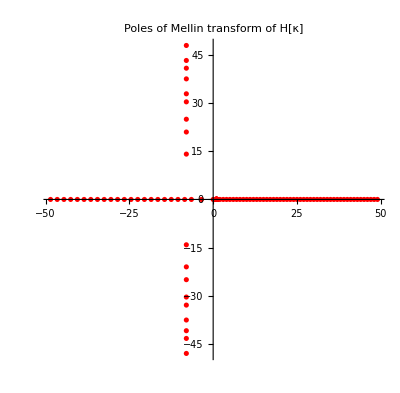

```mathematica
ComplexListPlot[pts, PlotStyle->{Red},PlotLabel->"Poles of Mellin transform of H[κ]"]
```

```mathematica
FunctionPoles[(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]),p]//TableForm
```

-17/2 | 1
-13/2 | 1
-7/2 | 1
ConditionalExpression[1/2 (-17-4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1+2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/2 (-17+2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

```mathematica
{a,b,c} = ABC[0.3]
```

{1.14196,0.00305917,0.0601122}

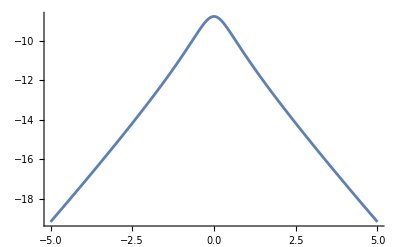

```mathematica
Plot[Re[Log[((20 c (-a c+b q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q])(0.1 c)^q)/.q->0.5+ I x]],{x,-5,5}, PlotRange->All]
```

```mathematica
Residue[(20 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q]),{q,0}]
```

-(20 A Zeta[15/2])/(119 Zeta[17/2])

```mathematica
HIntegral[A_, B_, C_,κ_, dt_] := TimeConstrained[Re[NIntegrate[((20 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q])κ^q)/.q->-0.5+ I x,
{x,-Infinity,Infinity},PrecisionGoal->6, Method->"DoubleExponentialOscillatory"]]/(2 Pi),dt];
```

```mathematica
HIntegral[a,b,c,0.1,1]//Timing
```

{0.075652,0.191727}

```mathematica
{0.147472,0.19172736546406138}
```

{0.147472,0.191727}

```mathematica
{0.152756,0.19172736546406138}
```

{0.152756,0.191727}

```mathematica
HIntegral[a,b,c,100,1]//Timing
```

{0.059483,0.00644511}

```mathematica
HIntegral[a,b,c,1000,1]//Timing
```

{0.053351,2.71845×10^-6}

```mathematica
HH[κ_] :=
Block[{ tab,OKtab, interp, delta = (Δ2 - Δ1)/100},
tab =(*Parallel*)Table[
Block[{A,B,C, ZI} ,
{A,B,C}= ABC[Δ];
(*Print[{Δ,{A,B,C}}];*)
ZI = HIntegral[A,B,C ,κ,1];
(*Print[{Δ,ZI}];*)
{Δ,Log[ZI]}], {Δ,Δ1, Δ2, delta}];
OKtab = Select[tab,NumericQ[#[[2]]]&];
If[Length[OKtab] < 10, Return[None]];
interp = Interpolation[OKtab,InterpolationOrder->5];
NIntegrate[(1-Δ)Exp[interp[Δ]],{Δ,Δ1, Δ2}]
]
```

```mathematica
HH[0.5]
```

0.0363317

```mathematica
htable[k0_, k1_, M_] := 
ParallelTable[
Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{k,HH[k]}]
,{n,0,M}];
```

```mathematica
htable[0.1,1,100]
```

{{0.1,0.0369082},{0.102329,0.0369048},{0.104713,0.0369013},{0.107152,0.0368978},{0.109648,0.0368942},{0.112202,0.0368904},{0.114815,0.0368866},{0.11749,0.0368828},{0.120226,0.0368788},{0.123027,0.0368747},{0.125893,0.0368706},{0.128825,0.0368663},{0.131826,0.036862},{0.134896,0.0368575},{0.138038,0.0368529},{0.141254,0.0368483},{0.144544,0.0368435},{0.147911,0.0368386},{0.151356,0.0368336},{0.154882,0.0368285},{0.158489,0.0368233},{0.162181,0.0368179},{0.165959,0.0368124},{0.169824,0.0368068},{0.17378,0.0368011},{0.177828,0.0367952},{0.18197,0.0367892},{0.186209,0.0367831},{0.190546,0.0367768},{0.194984,0.0367704},{0.199526,0.0367638},{0.204174,0.0367571},{0.20893,0.0367502},{0.213796,0.0367432},{0.218776,0.036736},{0.223872,0.0367286},{0.229087,0.0367211},{0.234423,0.0367134},{0.239883,0.0367055},{0.245471,0.0366974},{0.251189,0.0366891},{0.25704,0.0366807},{0.263027,0.036672},{0.269153,0.0366632},{0.275423,0.0366541},{0.281838,0.0366449},{0.288403,0.0366354},{0.295121,0.0366257},{0.301995,0.0366158},{0.30903,0.0366057},{0.316228,0.0365953},{0.323594,0.0365847},{0.331131,0.0365739},{0.338844,0.0365628},{0.346737,0.0365514},{0.354813,0.0365398},{0.363078,0.0365279},{0.371535,0.0365158},{0.380189,0.0365033},{0.389045,0.0364906},{0.398107,0.0364776},{0.40738,0.0364643},{0.416869,0.0364507},{0.42658,0.0364368},{0.436516,0.0364225},{0.446684,0.0364079},{0.457088,0.036393},{0.467735,0.0363778},{0.47863,0.0363622},{0.489779,0.0363463},{0.501187,0.03633},{0.512861,0.0363133},{0.524807,0.0362962},{0.537032,0.0362788},{0.549541,0.0362609},{0.562341,0.0362427},{0.57544,0.036224},{0.588844,0.0362049},{0.60256,0.0361854},{0.616595,0.0361654},{0.630957,0.036145},{0.645654,0.0361241},{0.660693,0.0361027},{0.676083,0.0360809},{0.691831,0.0360586},{0.707946,0.0360357},{0.724436,0.0360124},{0.74131,0.0359885},{0.758578,0.0359641},{0.776247,0.0359391},{0.794328,0.0359136},{0.812831,0.0358874},{0.831764,0.0358607},{0.851138,0.0358334},{0.870964,0.0358055},{0.891251,0.035777},{0.912011,0.0357478},{0.933254,0.035718},{0.954993,0.0356875},{0.977237,0.0356563},{1.,0.0356244}}

```mathematica
htab= htable[0.1,100,1000]
```

{{0.1,0.0369082},{0.100693,0.0369072},{0.101391,0.0369062},{0.102094,0.0369051},{0.102802,0.0369041},{0.103514,0.0369031},{0.104232,0.036902},{0.104954,0.036901},{0.105682,0.0368999},{0.106414,0.0368989},{0.107152,0.0368978},{0.107895,0.0368967},{0.108643,0.0368956},{0.109396,0.0368945},{0.110154,0.0368934},{0.110917,0.0368923},{0.111686,0.0368912},{0.11246,0.0368901},{0.11324,0.0368889},{0.114025,0.0368878},{0.114815,0.0368866},{0.115611,0.0368855},{0.116413,0.0368843},{0.11722,0.0368832},{0.118032,0.036882},{0.11885,0.0368808},{0.119674,0.0368796},{0.120504,0.0368784},{0.121339,0.0368772},{0.12218,0.036876},{0.123027,0.0368747},{0.12388,0.0368735},{0.124738,0.0368722},{0.125603,0.036871},{0.126474,0.0368697},{0.12735,0.0368684},{0.128233,0.0368672},{0.129122,0.0368659},{0.130017,0.0368646},{0.130918,0.0368633},{0.131826,0.036862},{0.132739,0.0368606},{0.13366,0.0368593},{0.134586,0.0368579},{0.135519,0.0368566},{0.136458,0.0368552},{0.137404,0.0368539},{0.138357,0.0368525},{0.139316,0.0368511},{0.140281,0.0368497},{0.141254,0.0368483},{0.142233,0.0368468},{0.143219,0.0368454},{0.144212,0.036844},{0.145211,0.0368425},{0.146218,0.0368411},{0.147231,0.0368396},{0.148252,0.0368381},{0.149279,0.0368366},{0.150314,0.0368351},{0.151356,0.0368336},{0.152405,0.0368321},{0.153462,0.0368306},{0.154525,0.036829},{0.155597,0.0368275},{0.156675,0.0368259},{0.157761,0.0368243},{0.158855,0.0368227},{0.159956,0.0368211},{0.161065,0.0368195},{0.162181,0.0368179},{0.163305,0.0368163},{0.164437,0.0368146},{0.165577,0.036813},{0.166725,0.0368113},{0.16788,0.0368097},{0.169044,0.036808},{0.170216,0.0368063},{0.171396,0.0368046},{0.172584,0.0368028},{0.17378,0.0368011},{0.174985,0.0367994},{0.176198,0.0367976},{0.177419,0.0367958},{0.178649,0.0367941},{0.179887,0.0367923},{0.181134,0.0367905},{0.18239,0.0367886},{0.183654,0.0367868},{0.184927,0.036785},{0.186209,0.0367831},{0.187499,0.0367812},{0.188799,0.0367794},{0.190108,0.0367775},{0.191426,0.0367756},{0.192752,0.0367736},{0.194089,0.0367717},{0.195434,0.0367697},{0.196789,0.0367678},{0.198153,0.0367658},{0.199526,0.0367638},{0.200909,0.0367618},{0.202302,0.0367598},{0.203704,0.0367578},{0.205116,0.0367557},{0.206538,0.0367537},{0.20797,0.0367516},{0.209411,0.0367495},{0.210863,0.0367474},{0.212324,0.0367453},{0.213796,0.0367432},{0.215278,0.036741},{0.21677,0.0367389},{0.218273,0.0367367},{0.219786,0.0367345},{0.221309,0.0367323},{0.222844,0.0367301},{0.224388,0.0367279},{0.225944,0.0367256},{0.22751,0.0367233},{0.229087,0.0367211},{0.230675,0.0367188},{0.232274,0.0367165},{0.233884,0.0367141},{0.235505,0.0367118},{0.237137,0.0367094},{0.238781,0.0367071},{0.240436,0.0367047},{0.242103,0.0367023},{0.243781,0.0366998},{0.245471,0.0366974},{0.247172,0.0366949},{0.248886,0.0366925},{0.250611,0.03669},{0.252348,0.0366875},{0.254097,0.0366849},{0.255859,0.0366824},{0.257632,0.0366798},{0.259418,0.0366772},{0.261216,0.0366747},{0.263027,0.036672},{0.26485,0.0366694},{0.266686,0.0366668},{0.268534,0.0366641},{0.270396,0.0366614},{0.27227,0.0366587},{0.274157,0.036656},{0.276058,0.0366532},{0.277971,0.0366505},{0.279898,0.0366477},{0.281838,0.0366449},{0.283792,0.0366421},{0.285759,0.0366392},{0.28774,0.0366364},{0.289734,0.0366335},{0.291743,0.0366306},{0.293765,0.0366277},{0.295801,0.0366248},{0.297852,0.0366218},{0.299916,0.0366188},{0.301995,0.0366158},{0.304089,0.0366128},{0.306196,0.0366098},{0.308319,0.0366067},{0.310456,0.0366036},{0.312608,0.0366005},{0.314775,0.0365974},{0.316957,0.0365943},{0.319154,0.0365911},{0.321366,0.0365879},{0.323594,0.0365847},{0.325837,0.0365815},{0.328095,0.0365782},{0.33037,0.036575},{0.33266,0.0365717},{0.334965,0.0365683},{0.337287,0.036565},{0.339625,0.0365616},{0.341979,0.0365583},{0.34435,0.0365548},{0.346737,0.0365514},{0.34914,0.036548},{0.35156,0.0365445},{0.353997,0.036541},{0.356451,0.0365374},{0.358922,0.0365339},{0.36141,0.0365303},{0.363915,0.0365267},{0.366438,0.0365231},{0.368978,0.0365194},{0.371535,0.0365158},{0.374111,0.0365121},{0.376704,0.0365083},{0.379315,0.0365046},{0.381944,0.0365008},{0.384592,0.036497},{0.387258,0.0364932},{0.389942,0.0364893},{0.392645,0.0364854},{0.395367,0.0364815},{0.398107,0.0364776},{0.400867,0.0364736},{0.403645,0.0364696},{0.406443,0.0364656},{0.409261,0.0364616},{0.412098,0.0364575},{0.414954,0.0364534},{0.41783,0.0364493},{0.420727,0.0364451},{0.423643,0.036441},{0.42658,0.0364368},{0.429536,0.0364325},{0.432514,0.0364282},{0.435512,0.0364239},{0.438531,0.0364196},{0.44157,0.0364153},{0.444631,0.0364109},{0.447713,0.0364065},{0.450817,0.036402},{0.453942,0.0363975},{0.457088,0.036393},{0.460257,0.0363885},{0.463447,0.0363839},{0.466659,0.0363793},{0.469894,0.0363747},{0.473151,0.03637},{0.476431,0.0363654},{0.479733,0.0363606},{0.483059,0.0363559},{0.486407,0.0363511},{0.489779,0.0363463},{0.493174,0.0363414},{0.496592,0.0363365},{0.500035,0.0363316},{0.503501,0.0363267},{0.506991,0.0363217},{0.510505,0.0363166},{0.514044,0.0363116},{0.517607,0.0363065},{0.521195,0.0363014},{0.524807,0.0362962},{0.528445,0.036291},{0.532108,0.0362858},{0.535797,0.0362805},{0.539511,0.0362752},{0.54325,0.0362699},{0.547016,0.0362645},{0.550808,0.0362591},{0.554626,0.0362537},{0.55847,0.0362482},{0.562341,0.0362427},{0.566239,0.0362371},{0.570164,0.0362315},{0.574116,0.0362259},{0.578096,0.0362202},{0.582103,0.0362145},{0.586138,0.0362088},{0.590201,0.036203},{0.594292,0.0361971},{0.598412,0.0361913},{0.60256,0.0361854},{0.606736,0.0361794},{0.610942,0.0361735},{0.615177,0.0361674},{0.619441,0.0361614},{0.623735,0.0361553},{0.628058,0.0361491},{0.632412,0.0361429},{0.636796,0.0361367},{0.64121,0.0361304},{0.645654,0.0361241},{0.65013,0.0361177},{0.654636,0.0361113},{0.659174,0.0361049},{0.663743,0.0360984},{0.668344,0.0360919},{0.672977,0.0360853},{0.677642,0.0360787},{0.682339,0.036072},{0.687068,0.0360653},{0.691831,0.0360586},{0.696627,0.0360518},{0.701455,0.0360449},{0.706318,0.036038},{0.711214,0.0360311},{0.716143,0.0360241},{0.721107,0.0360171},{0.726106,0.03601},{0.731139,0.0360029},{0.736207,0.0359957},{0.74131,0.0359885},{0.746449,0.0359812},{0.751623,0.0359739},{0.756833,0.0359665},{0.762079,0.0359591},{0.767361,0.0359517},{0.772681,0.0359441},{0.778037,0.0359366},{0.78343,0.0359289},{0.78886,0.0359213},{0.794328,0.0359136},{0.799834,0.0359058},{0.805378,0.035898},{0.810961,0.0358901},{0.816582,0.0358822},{0.822243,0.0358742},{0.827942,0.0358661},{0.833681,0.035858},{0.83946,0.0358499},{0.845279,0.0358417},{0.851138,0.0358334},{0.857038,0.0358251},{0.862979,0.0358168},{0.86896,0.0358084},{0.874984,0.0357999},{0.881049,0.0357913},{0.887156,0.0357828},{0.893305,0.0357741},{0.899498,0.0357654},{0.905733,0.0357566},{0.912011,0.0357478},{0.918333,0.0357389},{0.924698,0.03573},{0.931108,0.035721},{0.937562,0.0357119},{0.944061,0.0357028},{0.950605,0.0356936},{0.957194,0.0356844},{0.963829,0.0356751},{0.97051,0.0356657},{0.977237,0.0356563},{0.984011,0.0356468},{0.990832,0.0356373},{0.9977,0.0356277},{1.00462,0.035618},{1.01158,0.0356082},{1.01859,0.0355984},{1.02565,0.0355886},{1.03276,0.0355786},{1.03992,0.0355686},{1.04713,0.0355585},{1.05439,0.0355484},{1.0617,0.0355382},{1.06905,0.0355279},{1.07647,0.0355176},{1.08393,0.0355072},{1.09144,0.0354967},{1.09901,0.0354861},{1.10662,0.0354755},{1.11429,0.0354648},{1.12202,0.0354541},{1.1298,0.0354433},{1.13763,0.0354324},{1.14551,0.0354214},{1.15345,0.0354103},{1.16145,0.0353992},{1.1695,0.035388},{1.17761,0.0353768},{1.18577,0.0353654},{1.19399,0.035354},{1.20226,0.0353425},{1.2106,0.035331},{1.21899,0.0353193},{1.22744,0.0353076},{1.23595,0.0352958},{1.24451,0.0352839},{1.25314,0.035272},{1.26183,0.03526},{1.27057,0.0352479},{1.27938,0.0352357},{1.28825,0.0352234},{1.29718,0.0352111},{1.30617,0.0351986},{1.31522,0.0351861},{1.32434,0.0351735},{1.33352,0.0351609},{1.34276,0.0351481},{1.35207,0.0351353},{1.36144,0.0351223},{1.37088,0.0351093},{1.38038,0.0350962},{1.38995,0.0350831},{1.39959,0.0350698},{1.40929,0.0350564},{1.41906,0.035043},{1.42889,0.0350295},{1.4388,0.0350159},{1.44877,0.0350022},{1.45881,0.0349884},{1.46893,0.0349745},{1.47911,0.0349605},{1.48936,0.0349464},{1.49968,0.0349323},{1.51008,0.034918},{1.52055,0.0349037},{1.53109,0.0348893},{1.5417,0.0348747},{1.55239,0.0348601},{1.56315,0.0348454},{1.57398,0.0348306},{1.58489,0.0348157},{1.59588,0.0348007},{1.60694,0.0347856},{1.61808,0.0347704},{1.6293,0.0347551},{1.64059,0.0347397},{1.65196,0.0347242},{1.66341,0.0347086},{1.67494,0.0346929},{1.68655,0.0346771},{1.69824,0.0346612},{1.71002,0.0346452},{1.72187,0.0346291},{1.7338,0.0346129},{1.74582,0.0345966},{1.75792,0.0345802},{1.77011,0.0345637},{1.78238,0.0345471},{1.79473,0.0345303},{1.80717,0.0345135},{1.8197,0.0344965},{1.83231,0.0344795},{1.84502,0.0344623},{1.8578,0.034445},{1.87068,0.0344277},{1.88365,0.0344102},{1.89671,0.0343926},{1.90985,0.0343748},{1.92309,0.034357},{1.93642,0.0343391},{1.94984,0.034321},{1.96336,0.0343028},{1.97697,0.0342845},{1.99067,0.0342661},{2.00447,0.0342476},{2.01837,0.0342289},{2.03236,0.0342102},{2.04644,0.0341913},{2.06063,0.0341723},{2.07491,0.0341532},{2.0893,0.0341339},{2.10378,0.0341146},{2.11836,0.0340951},{2.13304,0.0340755},{2.14783,0.0340558},{2.16272,0.0340359},{2.17771,0.0340159},{2.1928,0.0339958},{2.208,0.0339756},{2.22331,0.0339552},{2.23872,0.0339347},{2.25424,0.0339141},{2.26986,0.0338934},{2.2856,0.0338725},{2.30144,0.0338515},{2.31739,0.0338303},{2.33346,0.0338091},{2.34963,0.0337877},{2.36592,0.0337661},{2.38232,0.0337444},{2.39883,0.0337226},{2.41546,0.0337007},{2.4322,0.0336786},{2.44906,0.0336564},{2.46604,0.033634},{2.48313,0.0336115},{2.50035,0.0335889},{2.51768,0.0335661},{2.53513,0.0335432},{2.5527,0.0335201},{2.5704,0.0334969},{2.58821,0.0334736},{2.60615,0.0334501},{2.62422,0.0334265},{2.64241,0.0334027},{2.66073,0.0333787},{2.67917,0.0333547},{2.69774,0.0333304},{2.71644,0.0333061},{2.73527,0.0332815},{2.75423,0.0332569},{2.77332,0.033232},{2.79254,0.0332071},{2.8119,0.0331819},{2.83139,0.0331567},{2.85102,0.0331312},{2.87078,0.0331056},{2.89068,0.0330799},{2.91072,0.033054},{2.93089,0.0330279},{2.95121,0.0330017},{2.97167,0.0329753},{2.99226,0.0329488},{3.01301,0.0329221},{3.03389,0.0328952},{3.05492,0.0328682},{3.0761,0.032841},{3.09742,0.0328136},{3.11889,0.0327861},{3.14051,0.0327584},{3.16228,0.0327306},{3.1842,0.0327025},{3.20627,0.0326743},{3.22849,0.032646},{3.25087,0.0326175},{3.27341,0.0325888},{3.2961,0.0325599},{3.31894,0.0325308},{3.34195,0.0325016},{3.36512,0.0324722},{3.38844,0.0324427},{3.41193,0.0324129},{3.43558,0.032383},{3.45939,0.0323529},{3.48337,0.0323226},{3.50752,0.0322922},{3.53183,0.0322615},{3.55631,0.0322307},{3.58096,0.0321997},{3.60579,0.0321685},{3.63078,0.0321372},{3.65595,0.0321056},{3.68129,0.0320739},{3.70681,0.032042},{3.7325,0.0320099},{3.75837,0.0319776},{3.78443,0.0319451},{3.81066,0.0319124},{3.83707,0.0318796},{3.86367,0.0318465},{3.89045,0.0318133},{3.91742,0.0317798},{3.94457,0.0317462},{3.97192,0.0317124},{3.99945,0.0316783},{4.02717,0.0316441},{4.05509,0.0316097},{4.08319,0.0315751},{4.1115,0.0315403},{4.14,0.0315052},{4.16869,0.03147},{4.19759,0.0314346},{4.22669,0.031399},{4.25598,0.0313632},{4.28549,0.0313271},{4.31519,0.0312909},{4.3451,0.0312545},{4.37522,0.0312178},{4.40555,0.031181},{4.43609,0.0311439},{4.46684,0.0311066},{4.4978,0.0310691},{4.52898,0.0310314},{4.56037,0.0309935},{4.59198,0.0309554},{4.62381,0.0309171},{4.65586,0.0308785},{4.68813,0.0308398},{4.72063,0.0308008},{4.75335,0.0307616},{4.7863,0.0307222},{4.81948,0.0306826},{4.85289,0.0306427},{4.88652,0.0306026},{4.9204,0.0305623},{4.9545,0.0305218},{4.98884,0.0304811},{5.02343,0.0304401},{5.05825,0.0303989},{5.09331,0.0303575},{5.12861,0.0303159},{5.16416,0.030274},{5.19996,0.0302319},{5.236,0.0301896},{5.2723,0.0301471},{5.30884,0.0301043},{5.34564,0.0300613},{5.3827,0.030018},{5.42001,0.0299745},{5.45758,0.0299308},{5.49541,0.0298869},{5.5335,0.0298427},{5.57186,0.0297983},{5.61048,0.0297536},{5.64937,0.0297088},{5.68853,0.0296636},{5.72796,0.0296183},{5.76766,0.0295727},{5.80764,0.0295268},{5.8479,0.0294807},{5.88844,0.0294344},{5.92925,0.0293878},{5.97035,0.029341},{6.01174,0.0292939},{6.05341,0.0292466},{6.09537,0.0291991},{6.13762,0.0291513},{6.18016,0.0291033},{6.223,0.029055},{6.26614,0.0290064},{6.30957,0.0289576},{6.35331,0.0289086},{6.39735,0.0288593},{6.44169,0.0288098},{6.48634,0.02876},{6.53131,0.0287099},{6.57658,0.0286596},{6.62217,0.0286091},{6.66807,0.0285583},{6.71429,0.0285072},{6.76083,0.0284559},{6.80769,0.0284044},{6.85488,0.0283525},{6.9024,0.0283005},{6.95024,0.0282481},{6.99842,0.0281955},{7.04693,0.0281427},{7.09578,0.0280895},{7.14496,0.0280362},{7.19449,0.0279825},{7.24436,0.0279286},{7.29458,0.0278745},{7.34514,0.0278201},{7.39605,0.0277654},{7.44732,0.0277104},{7.49894,0.0276552},{7.55092,0.0275997},{7.60326,0.027544},{7.65597,0.027488},{7.70903,0.0274317},{7.76247,0.0273752},{7.81628,0.0273184},{7.87046,0.0272613},{7.92501,0.027204},{7.97995,0.0271464},{8.03526,0.0270885},{8.09096,0.0270304},{8.14704,0.026972},{8.20352,0.0269133},{8.26038,0.0268544},{8.31764,0.0267952},{8.37529,0.0267357},{8.43335,0.026676},{8.4918,0.0266159},{8.55067,0.0265557},{8.60994,0.0264951},{8.66962,0.0264343},{8.72971,0.0263732},{8.79023,0.0263118},{8.85116,0.0262502},{8.91251,0.0261883},{8.97429,0.0261261},{9.03649,0.0260636},{9.09913,0.0260009},{9.1622,0.0259379},{9.22571,0.0258746},{9.28966,0.0258111},{9.35406,0.0257473},{9.4189,0.0256832},{9.48418,0.0256188},{9.54993,0.0255542},{9.61612,0.0254893},{9.68278,0.0254241},{9.7499,0.0253587},{9.81748,0.025293},{9.88553,0.025227},{9.95405,0.0251608},{10.0231,0.0250942},{10.0925,0.0250274},{10.1625,0.0249604},{10.2329,0.024893},{10.3039,0.0248254},{10.3753,0.0247575},{10.4472,0.0246894},{10.5196,0.024621},{10.5925,0.0245523},{10.666,0.0244833},{10.7399,0.0244141},{10.8143,0.0243446},{10.8893,0.0242749},{10.9648,0.0242048},{11.0408,0.0241346},{11.1173,0.024064},{11.1944,0.0239932},{11.272,0.0239221},{11.3501,0.0238507},{11.4288,0.0237791},{11.508,0.0237072},{11.5878,0.0236351},{11.6681,0.0235627},{11.749,0.02349},{11.8304,0.0234171},{11.9124,0.0233439},{11.995,0.0232705},{12.0781,0.0231968},{12.1619,0.0231228},{12.2462,0.0230486},{12.331,0.0229741},{12.4165,0.0228994},{12.5026,0.0228244},{12.5893,0.0227492},{12.6765,0.0226737},{12.7644,0.0225979},{12.8529,0.0225219},{12.942,0.0224457},{13.0317,0.0223692},{13.122,0.0222925},{13.213,0.0222155},{13.3045,0.0221382},{13.3968,0.0220608},{13.4896,0.0219831},{13.5831,0.0219051},{13.6773,0.0218269},{13.7721,0.0217485},{13.8676,0.0216698},{13.9637,0.0215909},{14.0605,0.0215117},{14.1579,0.0214324},{14.2561,0.0213527},{14.3549,0.0212729},{14.4544,0.0211928},{14.5546,0.0211125},{14.6555,0.021032},{14.7571,0.0209513},{14.8594,0.0208703},{14.9624,0.0207891},{15.0661,0.0207077},{15.1705,0.020626},{15.2757,0.0205442},{15.3815,0.0204621},{15.4882,0.0203799},{15.5955,0.0202974},{15.7036,0.0202147},{15.8125,0.0201318},{15.9221,0.0200487},{16.0325,0.0199654},{16.1436,0.0198818},{16.2555,0.0197981},{16.3682,0.0197142},{16.4816,0.0196301},{16.5959,0.0195458},{16.7109,0.0194614},{16.8267,0.0193767},{16.9434,0.0192918},{17.0608,0.0192068},{17.1791,0.0191216},{17.2982,0.0190362},{17.4181,0.0189506},{17.5388,0.0188648},{17.6604,0.0187789},{17.7828,0.0186928},{17.9061,0.0186065},{18.0302,0.0185201},{18.1552,0.0184335},{18.281,0.0183468},{18.4077,0.0182599},{18.5353,0.0181728},{18.6638,0.0180856},{18.7932,0.0179983},{18.9234,0.0179108},{19.0546,0.0178231},{19.1867,0.0177353},{19.3197,0.0176474},{19.4536,0.0175594},{19.5884,0.0174712},{19.7242,0.0173829},{19.8609,0.0172944},{19.9986,0.0172059},{20.1372,0.0171172},{20.2768,0.0170284},{20.4174,0.0169395},{20.5589,0.0168504},{20.7014,0.0167613},{20.8449,0.0166721},{20.9894,0.0165828},{21.1349,0.0164933},{21.2814,0.0164038},{21.4289,0.0163142},{21.5774,0.0162245},{21.727,0.0161347},{21.8776,0.0160449},{22.0293,0.0159549},{22.182,0.0158649},{22.3357,0.0157749},{22.4905,0.0156847},{22.6464,0.0155945},{22.8034,0.0155043},{22.9615,0.0154139},{23.1206,0.0153236},{23.2809,0.0152332},{23.4423,0.0151427},{23.6048,0.0150522},{23.7684,0.0149617},{23.9332,0.0148711},{24.0991,0.0147805},{24.2661,0.0146899},{24.4343,0.0145993},{24.6037,0.0145087},{24.7742,0.014418},{24.9459,0.0143273},{25.1189,0.0142367},{25.293,0.014146},{25.4683,0.0140553},{25.6448,0.0139647},{25.8226,0.013874},{26.0016,0.0137834},{26.1818,0.0136928},{26.3633,0.0136022},{26.5461,0.0135116},{26.7301,0.0134211},{26.9153,0.0133306},{27.1019,0.0132402},{27.2898,0.0131498},{27.4789,0.0130595},{27.6694,0.0129692},{27.8612,0.012879},{28.0543,0.0127888},{28.2488,0.0126987},{28.4446,0.0126087},{28.6418,0.0125187},{28.8403,0.0124289},{29.0402,0.0123391},{29.2415,0.0122494},{29.4442,0.0121598},{29.6483,0.0120703},{29.8538,0.011981},{30.0608,0.0118917},{30.2691,0.0118025},{30.4789,0.0117135},{30.6902,0.0116246},{30.903,0.0115358},{31.1172,0.0114471},{31.3329,0.0113586},{31.55,0.0112702},{31.7687,0.0111819},{31.989,0.0110938},{32.2107,0.0110059},{32.434,0.0109181},{32.6588,0.0108305},{32.8852,0.0107431},{33.1131,0.0106558},{33.3426,0.0105687},{33.5738,0.0104818},{33.8065,0.0103951},{34.0408,0.0103085},{34.2768,0.0102222},{34.5144,0.010136},{34.7536,0.0100501},{34.9945,0.00996439},{35.2371,0.00987888},{35.4813,0.00979359},{35.7273,0.00970852},{35.9749,0.00962368},{36.2243,0.00953907},{36.4754,0.0094547},{36.7282,0.00937057},{36.9828,0.00928669},{37.2392,0.00920305},{37.4973,0.00911967},{37.7572,0.00903655},{38.0189,0.00895369},{38.2825,0.00887111},{38.5478,0.00878879},{38.815,0.00870675},{39.0841,0.00862499},{39.355,0.00854352},{39.6278,0.00846233},{39.9025,0.00838144},{40.1791,0.00830085},{40.4576,0.00822056},{40.738,0.00814058},{41.0204,0.0080609},{41.3048,0.00798155},{41.5911,0.00790251},{41.8794,0.00782379},{42.1697,0.0077454},{42.462,0.00766734},{42.7563,0.00758962},{43.0527,0.00751223},{43.3511,0.00743519},{43.6516,0.00735849},{43.9542,0.00728215},{44.2588,0.00720615},{44.5656,0.00713052},{44.8745,0.00705525},{45.1856,0.00698034},{45.4988,0.0069058},{45.8142,0.00683163},{46.1318,0.00675784},{46.4515,0.00668443},{46.7735,0.0066114},{47.0977,0.00653875},{47.4242,0.0064665},{47.7529,0.00639463},{48.0839,0.00632317},{48.4172,0.0062521},{48.7528,0.00618143},{49.0908,0.00611117},{49.4311,0.00604131},{49.7737,0.00597187},{50.1187,0.00590284},{50.4661,0.00583423},{50.8159,0.00576604},{51.1682,0.00569827},{51.5229,0.00563092},{51.88,0.005564},{52.2396,0.00549751},{52.6017,0.00543145},{52.9663,0.00536583},{53.3335,0.00530064},{53.7032,0.0052359},{54.0754,0.00517159},{54.4503,0.00510773},{54.8277,0.00504432},{55.2077,0.00498135},{55.5904,0.00491883},{55.9758,0.00485677},{56.3638,0.00479515},{56.7545,0.004734},{57.1479,0.0046733},{57.544,0.00461305},{57.9429,0.00455327},{58.3445,0.00449395},{58.7489,0.00443509},{59.1562,0.0043767},{59.5662,0.00431877},{59.9791,0.00426131},{60.3949,0.00420432},{60.8135,0.0041478},{61.235,0.00409174},{61.6595,0.00403616},{62.0869,0.00398105},{62.5173,0.00392641},{62.9506,0.00387225},{63.387,0.00381855},{63.8263,0.00376534},{64.2688,0.00371259},{64.7143,0.00366033},{65.1628,0.00360854},{65.6145,0.00355722},{66.0693,0.00350638},{66.5273,0.00345602},{66.9885,0.00340613},{67.4528,0.00335672},{67.9204,0.00330778},{68.3912,0.00325932},{68.8652,0.00321134},{69.3426,0.00316383},{69.8232,0.00311679},{70.3072,0.00307023},{70.7946,0.00302415},{71.2853,0.00297854},{71.7794,0.0029334},{72.277,0.00288873},{72.778,0.00284453},{73.2825,0.0028008},{73.7904,0.00275755},{74.3019,0.00271476},{74.817,0.00267243},{75.3356,0.00263058},{75.8578,0.00258919},{76.3836,0.00254826},{76.913,0.00250779},{77.4462,0.00246779},{77.983,0.00242824},{78.5236,0.00238915},{79.0679,0.00235052},{79.6159,0.00231234},{80.1678,0.00227461},{80.7235,0.00223734},{81.2831,0.00220051},{81.8465,0.00216413},{82.4138,0.0021282},{82.9851,0.00209271},{83.5603,0.00205766},{84.1395,0.00202305},{84.7227,0.00198888},{85.31,0.00195514},{85.9014,0.00192183},{86.4968,0.00188895},{87.0964,0.0018565},{87.7001,0.00182448},{88.308,0.00179287},{88.9201,0.00176169},{89.5365,0.00173092},{90.1571,0.00170057},{90.7821,0.00167064},{91.4113,0.00164111},{92.045,0.00161198},{92.683,0.00158326},{93.3254,0.00155495},{93.9723,0.00152703},{94.6237,0.0014995},{95.2796,0.00147237},{95.9401,0.00144563},{96.6051,0.00141927},{97.2747,0.0013933},{97.949,0.0013677},{98.6279,0.00134248},{99.3116,0.00131764},{100.,0.00129317}}

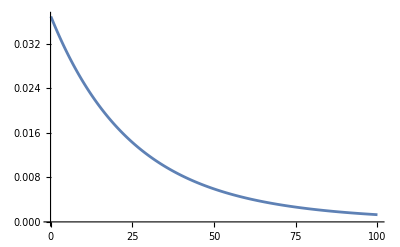

```mathematica
ListLinePlot[htab]
```

```mathematica
htab1= htable[100.1,1000,1000]
```

{{100.1,0.00128966},{100.331,0.0012816},{100.562,0.00127359},{100.794,0.00126562},{101.026,0.00125768},{101.259,0.00124979},{101.492,0.00124194},{101.726,0.00123413},{101.96,0.00122635},{102.195,0.00121862},{102.431,0.00121093},{102.667,0.00120327},{102.903,0.00119566},{103.14,0.00118808},{103.378,0.00118055},{103.616,0.00117305},{103.855,0.00116559},{104.094,0.00115817},{104.334,0.00115079},{104.575,0.00114345},{104.815,0.00113615},{105.057,0.00112888},{105.299,0.00112166},{105.542,0.00111447},{105.785,0.00110732},{106.029,0.0011002},{106.273,0.00109313},{106.518,0.00108609},{106.763,0.00107909},{107.009,0.00107212},{107.256,0.0010652},{107.503,0.00105831},{107.751,0.00105146},{107.999,0.00104464},{108.248,0.00103786},{108.497,0.00103112},{108.747,0.00102442},{108.998,0.00101775},{109.249,0.00101111},{109.501,0.00100452},{109.753,0.000997955},{110.006,0.00099143},{110.259,0.00098494},{110.514,0.000978486},{110.768,0.000972067},{111.023,0.000965683},{111.279,0.000959335},{111.536,0.000953021},{111.793,0.000946743},{112.05,0.000940499},{112.308,0.00093429},{112.567,0.000928115},{112.827,0.000921975},{113.087,0.000915869},{113.347,0.000909797},{113.608,0.000903759},{113.87,0.000897755},{114.133,0.000891785},{114.395,0.000885848},{114.659,0.000879945},{114.923,0.000874075},{115.188,0.000868239},{115.454,0.000862435},{115.72,0.000856665},{115.986,0.000850927},{116.253,0.000845222},{116.521,0.000839549},{116.79,0.000833909},{117.059,0.000828302},{117.329,0.000822726},{117.599,0.000817183},{117.87,0.000811671},{118.142,0.000806192},{118.414,0.000800744},{118.687,0.000795327},{118.96,0.000789942},{119.234,0.000784588},{119.509,0.000779266},{119.784,0.000773974},{120.06,0.000768713},{120.337,0.000763484},{120.614,0.000758284},{120.892,0.000753116},{121.171,0.000747977},{121.45,0.000742869},{121.73,0.000737791},{122.01,0.000732743},{122.292,0.000727725},{122.573,0.000722737},{122.856,0.000717778},{123.139,0.000712849},{123.423,0.000707949},{123.707,0.000703079},{123.992,0.000698237},{124.278,0.000693425},{124.564,0.000688641},{124.851,0.000683886},{125.139,0.00067916},{125.427,0.000674462},{125.716,0.000669793},{126.006,0.000665151},{126.296,0.000660538},{126.587,0.000655953},{126.879,0.000651396},{127.171,0.000646866},{127.464,0.000642364},{127.758,0.00063789},{128.052,0.000633443},{128.347,0.000629023},{128.643,0.00062463},{128.94,0.000620264},{129.237,0.000615925},{129.535,0.000611613},{129.833,0.000607327},{130.132,0.000603068},{130.432,0.000598835},{130.733,0.000594628},{131.034,0.000590447},{131.336,0.000586293},{131.638,0.000582164},{131.942,0.000578061},{132.246,0.000573984},{132.55,0.000569932},{132.856,0.000565905},{133.162,0.000561904},{133.469,0.000557928},{133.776,0.000553977},{134.085,0.00055005},{134.394,0.000546149},{134.703,0.000542272},{135.014,0.000538419},{135.325,0.000534591},{135.637,0.000530788},{135.949,0.000527008},{136.262,0.000523253},{136.576,0.000519521},{136.891,0.000515813},{137.206,0.000512129},{137.523,0.000508468},{137.84,0.000504831},{138.157,0.000501217},{138.475,0.000497627},{138.795,0.000494059},{139.114,0.000490514},{139.435,0.000486993},{139.756,0.000483494},{140.078,0.000480017},{140.401,0.000476563},{140.725,0.000473132},{141.049,0.000469723},{141.374,0.000466336},{141.7,0.000462971},{142.026,0.000459627},{142.353,0.000456306},{142.681,0.000453006},{143.01,0.000449728},{143.34,0.000446472},{143.67,0.000443237},{144.001,0.000440023},{144.333,0.00043683},{144.665,0.000433658},{144.999,0.000430507},{145.333,0.000427377},{145.668,0.000424267},{146.003,0.000421179},{146.34,0.00041811},{146.677,0.000415062},{147.015,0.000412034},{147.354,0.000409026},{147.693,0.000406039},{148.034,0.000403071},{148.375,0.000400123},{148.717,0.000397195},{149.059,0.000394286},{149.403,0.000391397},{149.747,0.000388527},{150.092,0.000385676},{150.438,0.000382845},{150.785,0.000380032},{151.132,0.000377239},{151.48,0.000374464},{151.829,0.000371708},{152.179,0.000368971},{152.53,0.000366252},{152.881,0.000363552},{153.234,0.00036087},{153.587,0.000358206},{153.941,0.00035556},{154.295,0.000352932},{154.651,0.000350323},{155.007,0.00034773},{155.364,0.000345156},{155.722,0.000342599},{156.081,0.00034006},{156.441,0.000337538},{156.801,0.000335034},{157.163,0.000332546},{157.525,0.000330076},{157.888,0.000327623},{158.251,0.000325186},{158.616,0.000322766},{158.982,0.000320363},{159.348,0.000317977},{159.715,0.000315607},{160.083,0.000313254},{160.452,0.000310917},{160.822,0.000308596},{161.192,0.000306291},{161.564,0.000304002},{161.936,0.000301729},{162.309,0.000299472},{162.683,0.000297231},{163.058,0.000295005},{163.434,0.000292795},{163.81,0.0002906},{164.188,0.000288421},{164.566,0.000286257},{164.945,0.000284108},{165.325,0.000281974},{165.706,0.000279855},{166.088,0.000277751},{166.471,0.000275662},{166.854,0.000273587},{167.239,0.000271527},{167.624,0.000269482},{168.01,0.000267451},{168.398,0.000265435},{168.786,0.000263433},{169.175,0.000261445},{169.564,0.000259471},{169.955,0.000257511},{170.347,0.000255565},{170.739,0.000253632},{171.133,0.000251714},{171.527,0.000249809},{171.922,0.000247918},{172.318,0.00024604},{172.715,0.000244176},{173.113,0.000242325},{173.512,0.000240487},{173.912,0.000238662},{174.313,0.000236851},{174.715,0.000235052},{175.117,0.000233267},{175.521,0.000231494},{175.925,0.000229734},{176.33,0.000227986},{176.737,0.000226251},{177.144,0.000224529},{177.552,0.000222819},{177.961,0.000221121},{178.371,0.000219436},{178.782,0.000217763},{179.194,0.000216102},{179.607,0.000214453},{180.021,0.000212816},{180.436,0.000211191},{180.852,0.000209577},{181.268,0.000207975},{181.686,0.000206385},{182.105,0.000204807},{182.524,0.00020324},{182.945,0.000201684},{183.366,0.00020014},{183.789,0.000198607},{184.212,0.000197085},{184.637,0.000195574},{185.062,0.000194075},{185.489,0.000192586},{185.916,0.000191108},{186.345,0.000189641},{186.774,0.000188185},{187.204,0.000186739},{187.636,0.000185304},{188.068,0.00018388},{188.501,0.000182466},{188.936,0.000181062},{189.371,0.000179669},{189.808,0.000178286},{190.245,0.000176914},{190.683,0.000175551},{191.123,0.000174198},{191.563,0.000172856},{192.004,0.000171523},{192.447,0.0001702},{192.89,0.000168887},{193.335,0.000167584},{193.78,0.00016629},{194.227,0.000165006},{194.674,0.000163732},{195.123,0.000162467},{195.572,0.000161211},{196.023,0.000159965},{196.475,0.000158728},{196.928,0.0001575},{197.381,0.000156281},{197.836,0.000155071},{198.292,0.000153871},{198.749,0.000152679},{199.207,0.000151496},{199.666,0.000150322},{200.126,0.000149157},{200.587,0.000148001},{201.049,0.000146853},{201.513,0.000145714},{201.977,0.000144583},{202.442,0.000143461},{202.909,0.000142347},{203.376,0.000141241},{203.845,0.000140144},{204.315,0.000139055},{204.785,0.000137975},{205.257,0.000136902},{205.73,0.000135837},{206.204,0.000134781},{206.679,0.000133732},{207.156,0.000132691},{207.633,0.000131659},{208.111,0.000130634},{208.591,0.000129616},{209.072,0.000128607},{209.553,0.000127605},{210.036,0.00012661},{210.52,0.000125623},{211.005,0.000124644},{211.492,0.000123672},{211.979,0.000122707},{212.467,0.000121749},{212.957,0.000120799},{213.448,0.000119856},{213.939,0.00011892},{214.432,0.000117992},{214.926,0.00011707},{215.422,0.000116155},{215.918,0.000115248},{216.416,0.000114347},{216.914,0.000113453},{217.414,0.000112566},{217.915,0.000111685},{218.417,0.000110812},{218.921,0.000109945},{219.425,0.000109084},{219.931,0.00010823},{220.437,0.000107383},{220.945,0.000106542},{221.454,0.000105708},{221.965,0.00010488},{222.476,0.000104058},{222.989,0.000103242},{223.503,0.000102433},{224.018,0.00010163},{224.534,0.000100833},{225.051,0.000100042},{225.57,0.0000992575},{226.09,0.0000984788},{226.61,0.000097706},{227.133,0.0000969391},{227.656,0.0000961782},{228.181,0.000095423},{228.706,0.0000946737},{229.233,0.0000939301},{229.762,0.0000931922},{230.291,0.00009246},{230.822,0.0000917335},{231.353,0.0000910125},{231.887,0.000090297},{232.421,0.0000895871},{232.956,0.0000888826},{233.493,0.0000881836},{234.031,0.0000874899},{234.571,0.0000868016},{235.111,0.0000861186},{235.653,0.0000854409},{236.196,0.0000847684},{236.74,0.000084101},{237.286,0.0000834389},{237.832,0.0000827818},{238.38,0.0000821298},{238.93,0.0000814829},{239.48,0.0000808409},{240.032,0.000080204},{240.585,0.0000795719},{241.139,0.0000789447},{241.695,0.0000783224},{242.252,0.0000777049},{242.81,0.0000770922},{243.37,0.0000764843},{243.93,0.000075881},{244.493,0.0000752824},{245.056,0.0000746885},{245.621,0.0000740991},{246.187,0.0000735144},{246.754,0.0000729341},{247.322,0.0000723584},{247.892,0.0000717872},{248.464,0.0000712203},{249.036,0.0000706579},{249.61,0.0000700999},{250.185,0.0000695462},{250.762,0.0000689968},{251.339,0.0000684516},{251.918,0.0000679107},{252.499,0.000067374},{253.081,0.0000668415},{253.664,0.0000663132},{254.248,0.0000657889},{254.834,0.0000652688},{255.421,0.0000647526},{256.01,0.0000642405},{256.6,0.0000637324},{257.191,0.0000632283},{257.784,0.0000627281},{258.378,0.0000622318},{258.973,0.0000617393},{259.57,0.0000612508},{260.168,0.000060766},{260.768,0.000060285},{261.368,0.0000598077},{261.971,0.0000593342},{262.574,0.0000588644},{263.179,0.0000583983},{263.786,0.0000579358},{264.394,0.0000574769},{265.003,0.0000570216},{265.613,0.0000565698},{266.225,0.0000561216},{266.839,0.0000556769},{267.454,0.0000552357},{268.07,0.000054798},{268.688,0.0000543636},{269.307,0.0000539327},{269.927,0.0000535051},{270.549,0.0000530809},{271.173,0.00005266},{271.798,0.0000522424},{272.424,0.0000518281},{273.052,0.0000514171},{273.681,0.0000510092},{274.311,0.0000506046},{274.944,0.0000502031},{275.577,0.0000498048},{276.212,0.0000494096},{276.849,0.0000490175},{277.486,0.0000486285},{278.126,0.0000482425},{278.767,0.0000478596},{279.409,0.0000474796},{280.053,0.0000471027},{280.698,0.0000467287},{281.345,0.0000463577},{281.993,0.0000459896},{282.643,0.0000456243},{283.294,0.000045262},{283.947,0.0000449025},{284.601,0.0000445458},{285.257,0.0000441919},{285.914,0.0000438408},{286.573,0.0000434925},{287.234,0.0000431469},{287.895,0.000042804},{288.559,0.0000424639},{289.224,0.0000421264},{289.89,0.0000417915},{290.558,0.0000414593},{291.228,0.0000411298},{291.899,0.0000408028},{292.571,0.0000404784},{293.246,0.0000401565},{293.921,0.0000398372},{294.598,0.0000395204},{295.277,0.0000392061},{295.958,0.0000388943},{296.64,0.0000385849},{297.323,0.000038278},{298.008,0.0000379735},{298.695,0.0000376714},{299.383,0.0000373717},{300.073,0.0000370744},{300.765,0.0000367794},{301.458,0.0000364867},{302.152,0.0000361963},{302.848,0.0000359083},{303.546,0.0000356225},{304.246,0.0000353389},{304.947,0.0000350576},{305.649,0.0000347786},{306.354,0.0000345017},{307.06,0.000034227},{307.767,0.0000339545},{308.476,0.0000336841},{309.187,0.0000334159},{309.9,0.0000331498},{310.614,0.0000328858},{311.329,0.0000326239},{312.047,0.0000323641},{312.766,0.0000321063},{313.486,0.0000318505},{314.209,0.0000315968},{314.933,0.0000313451},{315.658,0.0000310954},{316.386,0.0000308476},{317.115,0.0000306019},{317.846,0.000030358},{318.578,0.0000301161},{319.312,0.0000298761},{320.048,0.000029638},{320.785,0.0000294018},{321.524,0.0000291675},{322.265,0.000028935},{323.008,0.0000287044},{323.752,0.0000284756},{324.498,0.0000282486},{325.246,0.0000280234},{325.995,0.0000277999},{326.747,0.0000275783},{327.499,0.0000273584},{328.254,0.0000271403},{329.01,0.0000269238},{329.769,0.0000267091},{330.528,0.0000264961},{331.29,0.0000262848},{332.053,0.0000260752},{332.819,0.0000258672},{333.585,0.0000256609},{334.354,0.0000254562},{335.125,0.0000252532},{335.897,0.0000250517},{336.671,0.0000248519},{337.446,0.0000246536},{338.224,0.0000244569},{339.003,0.0000242618},{339.785,0.0000240682},{340.567,0.0000238761},{341.352,0.0000236856},{342.139,0.0000234966},{342.927,0.0000233091},{343.717,0.0000231231},{344.509,0.0000229385},{345.303,0.0000227555},{346.099,0.0000225738},{346.896,0.0000223937},{347.696,0.0000222149},{348.497,0.0000220376},{349.3,0.0000218617},{350.105,0.0000216872},{350.911,0.000021514},{351.72,0.0000213423},{352.53,0.0000211719},{353.343,0.0000210028},{354.157,0.0000208351},{354.973,0.0000206688},{355.791,0.0000205037},{356.611,0.00002034},{357.432,0.0000201776},{358.256,0.0000200164},{359.082,0.0000198566},{359.909,0.000019698},{360.738,0.0000195407},{361.57,0.0000193846},{362.403,0.0000192298},{363.238,0.0000190762},{364.075,0.0000189238},{364.914,0.0000187726},{365.755,0.0000186227},{366.597,0.0000184739},{367.442,0.0000183263},{368.289,0.0000181799},{369.137,0.0000180347},{369.988,0.0000178906},{370.84,0.0000177477},{371.695,0.0000176058},{372.551,0.0000174652},{373.41,0.0000173256},{374.27,0.0000171872},{375.133,0.0000170498},{375.997,0.0000169136},{376.863,0.0000167784},{377.732,0.0000166443},{378.602,0.0000165113},{379.475,0.0000163794},{380.349,0.0000162484},{381.225,0.0000161186},{382.104,0.0000159897},{382.984,0.0000158619},{383.867,0.0000157352},{384.751,0.0000156094},{385.638,0.0000154846},{386.526,0.0000153608},{387.417,0.000015238},{388.31,0.0000151162},{389.205,0.0000149954},{390.101,0.0000148755},{391.,0.0000147565},{391.901,0.0000146386},{392.804,0.0000145215},{393.709,0.0000144054},{394.617,0.0000142902},{395.526,0.000014176},{396.437,0.0000140626},{397.351,0.0000139502},{398.266,0.0000138386},{399.184,0.000013728},{400.104,0.0000136182},{401.026,0.0000135093},{401.95,0.0000134012},{402.876,0.0000132941},{403.804,0.0000131877},{404.735,0.0000130823},{405.667,0.0000129776},{406.602,0.0000128738},{407.539,0.0000127709},{408.478,0.0000126687},{409.419,0.0000125674},{410.363,0.0000124669},{411.308,0.0000123671},{412.256,0.0000122682},{413.206,0.0000121701},{414.158,0.0000120727},{415.113,0.0000119761},{416.069,0.0000118803},{417.028,0.0000117853},{417.989,0.000011691},{418.952,0.0000115975},{419.917,0.0000115047},{420.885,0.0000114126},{421.855,0.0000113213},{422.827,0.0000112307},{423.801,0.0000111409},{424.777,0.0000110517},{425.756,0.0000109633},{426.737,0.0000108756},{427.721,0.0000107885},{428.706,0.0000107022},{429.694,0.0000106166},{430.684,0.0000105316},{431.677,0.0000104473},{432.671,0.0000103637},{433.668,0.0000102808},{434.667,0.0000101985},{435.669,0.0000101169},{436.673,0.0000100359},{437.679,9.95561×10^-6},{438.688,9.87593×10^-6},{439.698,9.79689×10^-6},{440.712,9.71847×10^-6},{441.727,9.64069×10^-6},{442.745,9.56352×10^-6},{443.765,9.48697×10^-6},{444.788,9.41104×10^-6},{445.813,9.33571×10^-6},{446.84,9.26098×10^-6},{447.87,9.18685×10^-6},{448.902,9.11331×10^-6},{449.936,9.04036×10^-6},{450.973,8.96799×10^-6},{452.012,8.8962×10^-6},{453.053,8.82498×10^-6},{454.097,8.75433×10^-6},{455.144,8.68425×10^-6},{456.192,8.61472×10^-6},{457.244,8.54575×10^-6},{458.297,8.47734×10^-6},{459.353,8.40947×10^-6},{460.412,8.34214×10^-6},{461.473,8.27535×10^-6},{462.536,8.20909×10^-6},{463.602,8.14337×10^-6},{464.67,8.07816×10^-6},{465.741,8.01348×10^-6},{466.814,7.94932×10^-6},{467.889,7.88567×10^-6},{468.968,7.82253×10^-6},{470.048,7.75989×10^-6},{471.131,7.69775×10^-6},{472.217,7.63611×10^-6},{473.305,7.57497×10^-6},{474.396,7.51431×10^-6},{475.489,7.45413×10^-6},{476.584,7.39444×10^-6},{477.683,7.33523×10^-6},{478.783,7.27648×10^-6},{479.886,7.21821×10^-6},{480.992,7.16041×10^-6},{482.101,7.10306×10^-6},{483.211,7.04618×10^-6},{484.325,6.98975×10^-6},{485.441,6.93377×10^-6},{486.559,6.87823×10^-6},{487.681,6.82315×10^-6},{488.804,6.7685×10^-6},{489.931,6.71429×10^-6},{491.06,6.66051×10^-6},{492.191,6.60717×10^-6},{493.325,6.55425×10^-6},{494.462,6.50175×10^-6},{495.601,6.44967×10^-6},{496.743,6.39801×10^-6},{497.888,6.34676×10^-6},{499.035,6.29593×10^-6},{500.185,6.2455×10^-6},{501.338,6.19547×10^-6},{502.493,6.14584×10^-6},{503.651,6.09661×10^-6},{504.811,6.04777×10^-6},{505.974,5.99933×10^-6},{507.14,5.95127×10^-6},{508.309,5.9036×10^-6},{509.48,5.8563×10^-6},{510.654,5.80939×10^-6},{511.831,5.76285×10^-6},{513.01,5.71668×10^-6},{514.192,5.67089×10^-6},{515.377,5.62546×10^-6},{516.565,5.58039×10^-6},{517.755,5.53568×10^-6},{518.948,5.49133×10^-6},{520.144,5.44734×10^-6},{521.342,5.4037×10^-6},{522.543,5.3604×10^-6},{523.748,5.31746×10^-6},{524.954,5.27485×10^-6},{526.164,5.23259×10^-6},{527.376,5.19067×10^-6},{528.592,5.14908×10^-6},{529.81,5.10783×10^-6},{531.03,5.0669×10^-6},{532.254,5.0263×10^-6},{533.48,4.98603×10^-6},{534.71,4.94608×10^-6},{535.942,4.90645×10^-6},{537.177,4.86713×10^-6},{538.415,4.82813×10^-6},{539.655,4.78945×10^-6},{540.899,4.75107×10^-6},{542.145,4.713×10^-6},{543.394,4.67524×10^-6},{544.646,4.63777×10^-6},{545.901,4.60061×10^-6},{547.159,4.56374×10^-6},{548.42,4.52717×10^-6},{549.684,4.49089×10^-6},{550.95,4.45491×10^-6},{552.22,4.41921×10^-6},{553.492,4.38379×10^-6},{554.768,4.34866×10^-6},{556.046,4.31381×10^-6},{557.327,4.27924×10^-6},{558.611,4.24495×10^-6},{559.899,4.21093×10^-6},{561.189,4.17719×10^-6},{562.482,4.14371×10^-6},{563.778,4.1105×10^-6},{565.077,4.07756×10^-6},{566.379,4.04488×10^-6},{567.684,4.01246×10^-6},{568.992,3.98031×10^-6},{570.303,3.94841×10^-6},{571.617,3.91676×10^-6},{572.935,3.88537×10^-6},{574.255,3.85423×10^-6},{575.578,3.82334×10^-6},{576.904,3.7927×10^-6},{578.234,3.7623×10^-6},{579.566,3.73215×10^-6},{580.901,3.70223×10^-6},{582.24,3.67256×10^-6},{583.582,3.64313×10^-6},{584.926,3.61393×10^-6},{586.274,3.58496×10^-6},{587.625,3.55622×10^-6},{588.979,3.52772×10^-6},{590.336,3.49945×10^-6},{591.696,3.4714×10^-6},{593.06,3.44357×10^-6},{594.426,3.41597×10^-6},{595.796,3.38859×10^-6},{597.169,3.36143×10^-6},{598.545,3.33448×10^-6},{599.924,3.30776×10^-6},{601.307,3.28124×10^-6},{602.692,3.25494×10^-6},{604.081,3.22885×10^-6},{605.473,3.20297×10^-6},{606.868,3.17729×10^-6},{608.266,3.15182×10^-6},{609.668,3.12656×10^-6},{611.073,3.10149×10^-6},{612.481,3.07663×10^-6},{613.892,3.05197×10^-6},{615.307,3.0275×10^-6},{616.724,3.00323×10^-6},{618.146,2.97916×10^-6},{619.57,2.95528×10^-6},{620.998,2.93159×10^-6},{622.428,2.90809×10^-6},{623.863,2.88477×10^-6},{625.3,2.86165×10^-6},{626.741,2.83871×10^-6},{628.185,2.81595×10^-6},{629.633,2.79337×10^-6},{631.083,2.77098×10^-6},{632.538,2.74877×10^-6},{633.995,2.72673×10^-6},{635.456,2.70487×10^-6},{636.92,2.68319×10^-6},{638.388,2.66167×10^-6},{639.859,2.64034×10^-6},{641.333,2.61917×10^-6},{642.811,2.59817×10^-6},{644.292,2.57734×10^-6},{645.777,2.55668×10^-6},{647.265,2.53618×10^-6},{648.756,2.51585×10^-6},{650.251,2.49568×10^-6},{651.75,2.47567×10^-6},{653.251,2.45582×10^-6},{654.757,2.43613×10^-6},{656.265,2.4166×10^-6},{657.777,2.39722×10^-6},{659.293,2.378×10^-6},{660.812,2.35894×10^-6},{662.335,2.34002×10^-6},{663.861,2.32126×10^-6},{665.391,2.30265×10^-6},{666.924,2.28419×10^-6},{668.461,2.26587×10^-6},{670.001,2.24771×10^-6},{671.545,2.22969×10^-6},{673.092,2.21181×10^-6},{674.643,2.19407×10^-6},{676.198,2.17648×10^-6},{677.756,2.15903×10^-6},{679.318,2.14172×10^-6},{680.883,2.12455×10^-6},{682.452,2.10751×10^-6},{684.024,2.09061×10^-6},{685.601,2.07385×10^-6},{687.18,2.05722×10^-6},{688.764,2.04073×10^-6},{690.351,2.02436×10^-6},{691.942,2.00813×10^-6},{693.536,1.99203×10^-6},{695.134,1.97606×10^-6},{696.736,1.96021×10^-6},{698.341,1.94449×10^-6},{699.95,1.9289×10^-6},{701.563,1.91344×10^-6},{703.18,1.89809×10^-6},{704.8,1.88287×10^-6},{706.424,1.86777×10^-6},{708.052,1.8528×10^-6},{709.683,1.83794×10^-6},{711.319,1.8232×10^-6},{712.958,1.80858×10^-6},{714.601,1.79408×10^-6},{716.247,1.77969×10^-6},{717.898,1.76542×10^-6},{719.552,1.75127×10^-6},{721.21,1.73722×10^-6},{722.872,1.72329×10^-6},{724.537,1.70947×10^-6},{726.207,1.69576×10^-6},{727.88,1.68217×10^-6},{729.557,1.66868×10^-6},{731.238,1.6553×10^-6},{732.923,1.64202×10^-6},{734.612,1.62885×10^-6},{736.305,1.61579×10^-6},{738.002,1.60283×10^-6},{739.702,1.58998×10^-6},{741.407,1.57723×10^-6},{743.115,1.56458×10^-6},{744.827,1.55204×10^-6},{746.544,1.53959×10^-6},{748.264,1.52724×10^-6},{749.988,1.515×10^-6},{751.716,1.50285×10^-6},{753.448,1.49079×10^-6},{755.184,1.47884×10^-6},{756.924,1.46698×10^-6},{758.669,1.45521×10^-6},{760.417,1.44354×10^-6},{762.169,1.43197×10^-6},{763.925,1.42048×10^-6},{765.685,1.40909×10^-6},{767.45,1.39779×10^-6},{769.218,1.38658×10^-6},{770.991,1.37546×10^-6},{772.767,1.36443×10^-6},{774.548,1.35349×10^-6},{776.332,1.34263×10^-6},{778.121,1.33187×10^-6},{779.914,1.32119×10^-6},{781.711,1.31059×10^-6},{783.513,1.30008×10^-6},{785.318,1.28965×10^-6},{787.128,1.27931×10^-6},{788.941,1.26905×10^-6},{790.759,1.25887×10^-6},{792.581,1.24878×10^-6},{794.408,1.23876×10^-6},{796.238,1.22883×10^-6},{798.073,1.21897×10^-6},{799.912,1.20919×10^-6},{801.755,1.1995×10^-6},{803.602,1.18988×10^-6},{805.454,1.18033×10^-6},{807.31,1.17087×10^-6},{809.17,1.16148×10^-6},{811.035,1.15216×10^-6},{812.904,1.14292×10^-6},{814.777,1.13375×10^-6},{816.654,1.12466×10^-6},{818.536,1.11564×10^-6},{820.422,1.10669×10^-6},{822.313,1.09782×10^-6},{824.207,1.08901×10^-6},{826.106,1.08028×10^-6},{828.01,1.07161×10^-6},{829.918,1.06302×10^-6},{831.83,1.05449×10^-6},{833.747,1.04604×10^-6},{835.668,1.03765×10^-6},{837.594,1.02932×10^-6},{839.524,1.02107×10^-6},{841.458,1.01288×10^-6},{843.397,1.00475×10^-6},{845.341,9.96696×10^-7},{847.288,9.88702×10^-7},{849.241,9.80772×10^-7},{851.198,9.72906×10^-7},{853.159,9.65102×10^-7},{855.125,9.57362×10^-7},{857.095,9.49683×10^-7},{859.07,9.42066×10^-7},{861.05,9.3451×10^-7},{863.034,9.27014×10^-7},{865.022,9.19579×10^-7},{867.016,9.12203×10^-7},{869.013,9.04887×10^-7},{871.016,8.97629×10^-7},{873.023,8.90429×10^-7},{875.035,8.83287×10^-7},{877.051,8.76203×10^-7},{879.072,8.69175×10^-7},{881.097,8.62203×10^-7},{883.128,8.55288×10^-7},{885.162,8.48427×10^-7},{887.202,8.41622×10^-7},{889.246,8.34872×10^-7},{891.295,8.28175×10^-7},{893.349,8.21532×10^-7},{895.408,8.14943×10^-7},{897.471,8.08406×10^-7},{899.539,8.01922×10^-7},{901.612,7.9549×10^-7},{903.689,7.89109×10^-7},{905.772,7.8278×10^-7},{907.859,7.76501×10^-7},{909.951,7.70273×10^-7},{912.047,7.64094×10^-7},{914.149,7.57965×10^-7},{916.255,7.51886×10^-7},{918.367,7.45855×10^-7},{920.483,7.39872×10^-7},{922.604,7.33937×10^-7},{924.73,7.2805×10^-7},{926.86,7.22211×10^-7},{928.996,7.16418×10^-7},{931.137,7.10671×10^-7},{933.282,7.04971×10^-7},{935.433,6.99316×10^-7},{937.588,6.93706×10^-7},{939.749,6.88142×10^-7},{941.914,6.82622×10^-7},{944.084,6.77147×10^-7},{946.26,6.71715×10^-7},{948.44,6.66327×10^-7},{950.626,6.60982×10^-7},{952.816,6.5568×10^-7},{955.012,6.50421×10^-7},{957.212,6.45204×10^-7},{959.418,6.40028×10^-7},{961.629,6.34894×10^-7},{963.844,6.29802×10^-7},{966.065,6.2475×10^-7},{968.291,6.19738×10^-7},{970.523,6.14767×10^-7},{972.759,6.09836×10^-7},{975.,6.04944×10^-7},{977.247,6.00091×10^-7},{979.499,5.95278×10^-7},{981.756,5.90503×10^-7},{984.018,5.85766×10^-7},{986.285,5.81067×10^-7},{988.558,5.76406×10^-7},{990.836,5.71783×10^-7},{993.119,5.67196×10^-7},{995.407,5.62646×10^-7},{997.701,5.58133×10^-7},{1000.,5.53656×10^-7}}

```mathematica
htab01 = Join[htab, htab1];
```

```mathematica
Dimensions[htab01]
```

{}

```mathematica
lhinterp=Interpolation@Log[htab01];
```

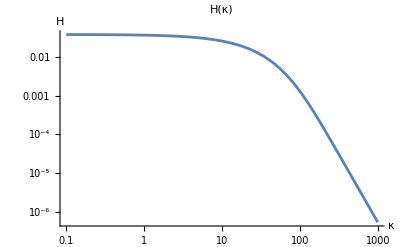

```mathematica
LogLogPlot[Exp[lhinterp[Log[k]]],{k,0.1,1000}, PlotLabel->"H(κ)", AxesLabel->{κ, H}]
```

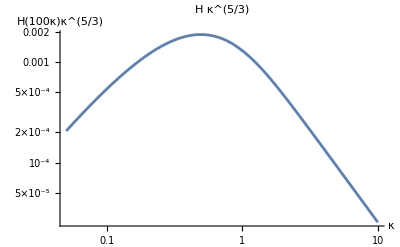

```mathematica
LogLogPlot[Exp[lhinterp[Log[100k]]+ 5/3 Log[k]],{k,0.05,10}, PlotLabel->"H κ^(5/3)", AxesLabel->{κ, "H(100κ)κ^(5/3)"}]
```

```mathematica
SPIndex[κ_]:= Evaluate[-D[lhinterp[t],t]/.t->Log[κ]];
```

```mathematica
SPIndex[1000.]
```

3.4993

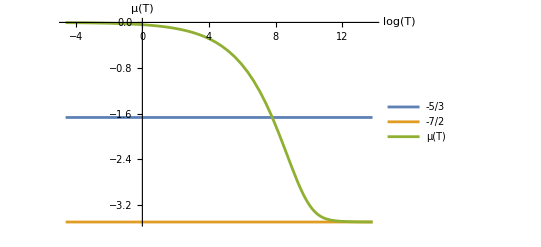

```mathematica
Plot[{-5/3,-7/2,-SPIndex[Exp[x/2]]},{x,Log[0.01],Log[10^6]}, 
PlotLegends->{-5/3,-7/2,μ[T]},
AxesLabel->{Log[T], μ[T]}]
```

```mathematica
EDis[t_] := With[{x0=1000},(NIntegrate[Exp[lhinterp[Log[x]]] x^2 ,{x, Sqrt[t],x0}] + 
Exp[lhinterp[Log[x0]]]2 x0^3)]
```

```mathematica
EDis[0]
```

4499.66

```mathematica
etable[k0_, k1_, M_] := 
ParallelTable[
Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{k,EDis[k^2]}]
,{n,0,M}];
```

```mathematica
etab = etable[0.1, 1000, 1000];
```

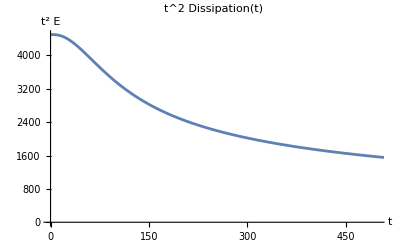

```mathematica
ListLinePlot[etab, PlotLabel->"t^2 Dissipation(t) ", AxesLabel->{t,t^2 Ε}]
```

```mathematica
einterp = Interpolation[{#[[1]],Log[#[[2]]]} &/@etab];
```

```mathematica
EEAll[t_] :=Exp[einterp[Sqrt[t]]]/t^2;
```

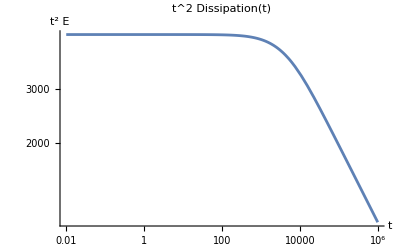

```mathematica
LogLogPlot[Exp[einterp[Sqrt[t]]],{t,0.1^2,1000^2}, PlotLabel->"t^2 Dissipation(t)", AxesLabel->{t,t^2 Ε}, PlotRange->All]
```

```mathematica
einterp[0]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

8.41176

```mathematica
x = .;
```

```mathematica
n[t_] :=Evaluate[1 - 1/2x D[einterp[x],x]/.x->Sqrt[t]];
```

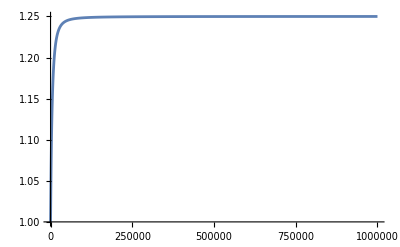

```mathematica
Plot[n[t],{t,0.1^2,1000^2}, PlotRange->All]
```

```mathematica
FindMinimum[{n[z], 0.1^2 < z < 1000^2},z]
```

{1.,{z→0.0801557}}

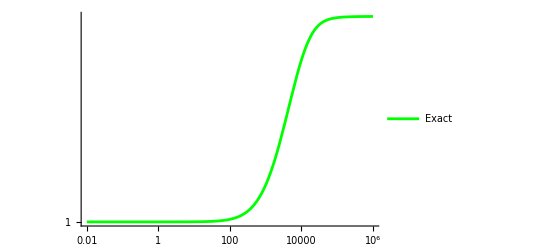

```mathematica
P1 =LogLogPlot[n[t],{t,0.1^2,1000^2}, PlotStyle->Green,PlotLegends->{"Exact"}, PlotRange->All]
```

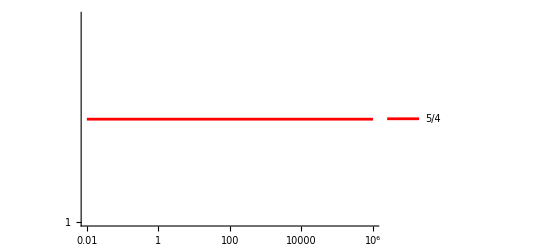

```mathematica
P2 = LogLogPlot[5/4,{t,0.1^2,1000^2}, PlotStyle->Red, PlotLegends->{5/4}]
```

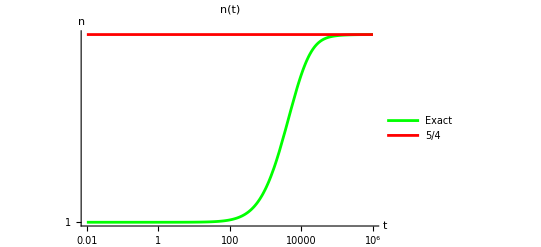

```mathematica
Show[{P1,P2}, PlotLabel->"n(t)", AxesLabel->{t, n}]
```

```mathematica
TailE = Integrate[(1/x)^(9/4),{x,t0, Infinity}, GenerateConditions->False]
```

4/5 (1/t0)^(5/4)

```mathematica
EDec[t_] :=With[{t0 = 1000^2},NIntegrate[EEAll[x],{x,t,t0}] + EEAll[t0]4/5 t0];
```

```mathematica
EDec[1000]
```

3.97548

```mathematica
edectable[k0_, k1_, M_] :=  
ParallelTable[Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{Log[k^2], Log[k^2 EDec[k^2]]}]
,{n,0,M}];
```

```mathematica
edectab =edectable[0.1, 1000,1000]
```

{{-4.60517,8.41175},{-4.58675,8.41175},{-4.56833,8.41175},{-4.54991,8.41175},{-4.53149,8.41175},{-4.51307,8.41175},{-4.49465,8.41175},{-4.47623,8.41175},{-4.4578,8.41175},{-4.43938,8.41175},{-4.42096,8.41175},{-4.40254,8.41175},{-4.38412,8.41175},{-4.3657,8.41175},{-4.34728,8.41175},{-4.32886,8.41175},{-4.31044,8.41175},{-4.29202,8.41175},{-4.2736,8.41175},{-4.25518,8.41175},{-4.23676,8.41175},{-4.21834,8.41175},{-4.19992,8.41175},{-4.18149,8.41175},{-4.16307,8.41175},{-4.14465,8.41175},{-4.12623,8.41175},{-4.10781,8.41175},{-4.08939,8.41175},{-4.07097,8.41175},{-4.05255,8.41175},{-4.03413,8.41175},{-4.01571,8.41175},{-3.99729,8.41175},{-3.97887,8.41175},{-3.96045,8.41175},{-3.94203,8.41175},{-3.9236,8.41175},{-3.90518,8.41175},{-3.88676,8.41175},{-3.86834,8.41175},{-3.84992,8.41175},{-3.8315,8.41175},{-3.81308,8.41175},{-3.79466,8.41175},{-3.77624,8.41175},{-3.75782,8.41175},{-3.7394,8.41175},{-3.72098,8.41175},{-3.70256,8.41175},{-3.68414,8.41175},{-3.66572,8.41175},{-3.64729,8.41175},{-3.62887,8.41175},{-3.61045,8.41175},{-3.59203,8.41175},{-3.57361,8.41175},{-3.55519,8.41175},{-3.53677,8.41175},{-3.51835,8.41175},{-3.49993,8.41175},{-3.48151,8.41175},{-3.46309,8.41175},{-3.44467,8.41175},{-3.42625,8.41175},{-3.40783,8.41175},{-3.38941,8.41175},{-3.37098,8.41175},{-3.35256,8.41175},{-3.33414,8.41175},{-3.31572,8.41175},{-3.2973,8.41175},{-3.27888,8.41175},{-3.26046,8.41175},{-3.24204,8.41175},{-3.22362,8.41175},{-3.2052,8.41175},{-3.18678,8.41175},{-3.16836,8.41175},{-3.14994,8.41175},{-3.13152,8.41175},{-3.1131,8.41175},{-3.09467,8.41175},{-3.07625,8.41175},{-3.05783,8.41175},{-3.03941,8.41175},{-3.02099,8.41175},{-3.00257,8.41175},{-2.98415,8.41175},{-2.96573,8.41175},{-2.94731,8.41175},{-2.92889,8.41174},{-2.91047,8.41174},{-2.89205,8.41174},{-2.87363,8.41174},{-2.85521,8.41174},{-2.83678,8.41174},{-2.81836,8.41174},{-2.79994,8.41174},{-2.78152,8.41174},{-2.7631,8.41174},{-2.74468,8.41174},{-2.72626,8.41174},{-2.70784,8.41174},{-2.68942,8.41174},{-2.671,8.41174},{-2.65258,8.41174},{-2.63416,8.41174},{-2.61574,8.41174},{-2.59732,8.41174},{-2.5789,8.41174},{-2.56047,8.41174},{-2.54205,8.41174},{-2.52363,8.41174},{-2.50521,8.41174},{-2.48679,8.41174},{-2.46837,8.41174},{-2.44995,8.41174},{-2.43153,8.41174},{-2.41311,8.41174},{-2.39469,8.41174},{-2.37627,8.41174},{-2.35785,8.41174},{-2.33943,8.41174},{-2.32101,8.41173},{-2.30259,8.41173},{-2.28416,8.41173},{-2.26574,8.41173},{-2.24732,8.41173},{-2.2289,8.41173},{-2.21048,8.41173},{-2.19206,8.41173},{-2.17364,8.41173},{-2.15522,8.41173},{-2.1368,8.41173},{-2.11838,8.41173},{-2.09996,8.41173},{-2.08154,8.41173},{-2.06312,8.41173},{-2.0447,8.41173},{-2.02627,8.41173},{-2.00785,8.41173},{-1.98943,8.41173},{-1.97101,8.41173},{-1.95259,8.41172},{-1.93417,8.41172},{-1.91575,8.41172},{-1.89733,8.41172},{-1.87891,8.41172},{-1.86049,8.41172},{-1.84207,8.41172},{-1.82365,8.41172},{-1.80523,8.41172},{-1.78681,8.41172},{-1.76839,8.41172},{-1.74996,8.41172},{-1.73154,8.41172},{-1.71312,8.41172},{-1.6947,8.41172},{-1.67628,8.41171},{-1.65786,8.41171},{-1.63944,8.41171},{-1.62102,8.41171},{-1.6026,8.41171},{-1.58418,8.41171},{-1.56576,8.41171},{-1.54734,8.41171},{-1.52892,8.41171},{-1.5105,8.41171},{-1.49208,8.41171},{-1.47365,8.4117},{-1.45523,8.4117},{-1.43681,8.4117},{-1.41839,8.4117},{-1.39997,8.4117},{-1.38155,8.4117},{-1.36313,8.4117},{-1.34471,8.4117},{-1.32629,8.4117},{-1.30787,8.4117},{-1.28945,8.41169},{-1.27103,8.41169},{-1.25261,8.41169},{-1.23419,8.41169},{-1.21576,8.41169},{-1.19734,8.41169},{-1.17892,8.41169},{-1.1605,8.41169},{-1.14208,8.41168},{-1.12366,8.41168},{-1.10524,8.41168},{-1.08682,8.41168},{-1.0684,8.41168},{-1.04998,8.41168},{-1.03156,8.41168},{-1.01314,8.41167},{-0.994717,8.41167},{-0.976296,8.41167},{-0.957875,8.41167},{-0.939455,8.41167},{-0.921034,8.41167},{-0.902613,8.41166},{-0.884193,8.41166},{-0.865772,8.41166},{-0.847351,8.41166},{-0.828931,8.41166},{-0.81051,8.41166},{-0.792089,8.41165},{-0.773669,8.41165},{-0.755248,8.41165},{-0.736827,8.41165},{-0.718407,8.41165},{-0.699986,8.41164},{-0.681565,8.41164},{-0.663145,8.41164},{-0.644724,8.41164},{-0.626303,8.41164},{-0.607882,8.41163},{-0.589462,8.41163},{-0.571041,8.41163},{-0.55262,8.41163},{-0.5342,8.41162},{-0.515779,8.41162},{-0.497358,8.41162},{-0.478938,8.41162},{-0.460517,8.41161},{-0.442096,8.41161},{-0.423676,8.41161},{-0.405255,8.41161},{-0.386834,8.4116},{-0.368414,8.4116},{-0.349993,8.4116},{-0.331572,8.41159},{-0.313152,8.41159},{-0.294731,8.41159},{-0.27631,8.41159},{-0.25789,8.41158},{-0.239469,8.41158},{-0.221048,8.41158},{-0.202627,8.41157},{-0.184207,8.41157},{-0.165786,8.41157},{-0.147365,8.41156},{-0.128945,8.41156},{-0.110524,8.41155},{-0.0921034,8.41155},{-0.0736827,8.41155},{-0.055262,8.41154},{-0.0368414,8.41154},{-0.0184207,8.41154},{0.,8.41153},{0.0184207,8.41153},{0.0368414,8.41152},{0.055262,8.41152},{0.0736827,8.41151},{0.0921034,8.41151},{0.110524,8.41151},{0.128945,8.4115},{0.147365,8.4115},{0.165786,8.41149},{0.184207,8.41149},{0.202627,8.41148},{0.221048,8.41148},{0.239469,8.41147},{0.25789,8.41147},{0.27631,8.41146},{0.294731,8.41146},{0.313152,8.41145},{0.331572,8.41144},{0.349993,8.41144},{0.368414,8.41143},{0.386834,8.41143},{0.405255,8.41142},{0.423676,8.41141},{0.442096,8.41141},{0.460517,8.4114},{0.478938,8.4114},{0.497358,8.41139},{0.515779,8.41138},{0.5342,8.41137},{0.55262,8.41137},{0.571041,8.41136},{0.589462,8.41135},{0.607882,8.41135},{0.626303,8.41134},{0.644724,8.41133},{0.663145,8.41132},{0.681565,8.41132},{0.699986,8.41131},{0.718407,8.4113},{0.736827,8.41129},{0.755248,8.41128},{0.773669,8.41127},{0.792089,8.41126},{0.81051,8.41126},{0.828931,8.41125},{0.847351,8.41124},{0.865772,8.41123},{0.884193,8.41122},{0.902613,8.41121},{0.921034,8.4112},{0.939455,8.41119},{0.957875,8.41118},{0.976296,8.41117},{0.994717,8.41116},{1.01314,8.41115},{1.03156,8.41113},{1.04998,8.41112},{1.0684,8.41111},{1.08682,8.4111},{1.10524,8.41109},{1.12366,8.41108},{1.14208,8.41106},{1.1605,8.41105},{1.17892,8.41104},{1.19734,8.41102},{1.21576,8.41101},{1.23419,8.411},{1.25261,8.41098},{1.27103,8.41097},{1.28945,8.41095},{1.30787,8.41094},{1.32629,8.41093},{1.34471,8.41091},{1.36313,8.41089},{1.38155,8.41088},{1.39997,8.41086},{1.41839,8.41085},{1.43681,8.41083},{1.45523,8.41081},{1.47365,8.4108},{1.49208,8.41078},{1.5105,8.41076},{1.52892,8.41074},{1.54734,8.41073},{1.56576,8.41071},{1.58418,8.41069},{1.6026,8.41067},{1.62102,8.41065},{1.63944,8.41063},{1.65786,8.41061},{1.67628,8.41059},{1.6947,8.41057},{1.71312,8.41054},{1.73154,8.41052},{1.74996,8.4105},{1.76839,8.41048},{1.78681,8.41045},{1.80523,8.41043},{1.82365,8.41041},{1.84207,8.41038},{1.86049,8.41036},{1.87891,8.41033},{1.89733,8.41031},{1.91575,8.41028},{1.93417,8.41025},{1.95259,8.41023},{1.97101,8.4102},{1.98943,8.41017},{2.00785,8.41014},{2.02627,8.41011},{2.0447,8.41008},{2.06312,8.41005},{2.08154,8.41002},{2.09996,8.40999},{2.11838,8.40996},{2.1368,8.40993},{2.15522,8.40989},{2.17364,8.40986},{2.19206,8.40983},{2.21048,8.40979},{2.2289,8.40976},{2.24732,8.40972},{2.26574,8.40969},{2.28416,8.40965},{2.30259,8.40961},{2.32101,8.40957},{2.33943,8.40953},{2.35785,8.40949},{2.37627,8.40945},{2.39469,8.40941},{2.41311,8.40937},{2.43153,8.40933},{2.44995,8.40928},{2.46837,8.40924},{2.48679,8.40919},{2.50521,8.40915},{2.52363,8.4091},{2.54205,8.40905},{2.56047,8.40901},{2.5789,8.40896},{2.59732,8.40891},{2.61574,8.40886},{2.63416,8.4088},{2.65258,8.40875},{2.671,8.4087},{2.68942,8.40864},{2.70784,8.40859},{2.72626,8.40853},{2.74468,8.40847},{2.7631,8.40842},{2.78152,8.40836},{2.79994,8.4083},{2.81836,8.40824},{2.83678,8.40817},{2.85521,8.40811},{2.87363,8.40804},{2.89205,8.40798},{2.91047,8.40791},{2.92889,8.40784},{2.94731,8.40778},{2.96573,8.4077},{2.98415,8.40763},{3.00257,8.40756},{3.02099,8.40749},{3.03941,8.40741},{3.05783,8.40733},{3.07625,8.40726},{3.09467,8.40718},{3.1131,8.4071},{3.13152,8.40701},{3.14994,8.40693},{3.16836,8.40685},{3.18678,8.40676},{3.2052,8.40667},{3.22362,8.40658},{3.24204,8.40649},{3.26046,8.4064},{3.27888,8.40631},{3.2973,8.40621},{3.31572,8.40611},{3.33414,8.40601},{3.35256,8.40591},{3.37098,8.40581},{3.38941,8.40571},{3.40783,8.4056},{3.42625,8.40549},{3.44467,8.40539},{3.46309,8.40527},{3.48151,8.40516},{3.49993,8.40505},{3.51835,8.40493},{3.53677,8.40481},{3.55519,8.40469},{3.57361,8.40457},{3.59203,8.40444},{3.61045,8.40432},{3.62887,8.40419},{3.64729,8.40405},{3.66572,8.40392},{3.68414,8.40379},{3.70256,8.40365},{3.72098,8.40351},{3.7394,8.40337},{3.75782,8.40322},{3.77624,8.40307},{3.79466,8.40292},{3.81308,8.40277},{3.8315,8.40262},{3.84992,8.40246},{3.86834,8.4023},{3.88676,8.40214},{3.90518,8.40197},{3.9236,8.4018},{3.94203,8.40163},{3.96045,8.40146},{3.97887,8.40128},{3.99729,8.4011},{4.01571,8.40092},{4.03413,8.40074},{4.05255,8.40055},{4.07097,8.40036},{4.08939,8.40016},{4.10781,8.39996},{4.12623,8.39976},{4.14465,8.39956},{4.16307,8.39935},{4.18149,8.39914},{4.19992,8.39893},{4.21834,8.39871},{4.23676,8.39849},{4.25518,8.39826},{4.2736,8.39804},{4.29202,8.3978},{4.31044,8.39757},{4.32886,8.39733},{4.34728,8.39708},{4.3657,8.39684},{4.38412,8.39659},{4.40254,8.39633},{4.42096,8.39607},{4.43938,8.39581},{4.4578,8.39554},{4.47623,8.39527},{4.49465,8.39499},{4.51307,8.39471},{4.53149,8.39443},{4.54991,8.39414},{4.56833,8.39384},{4.58675,8.39355},{4.60517,8.39324},{4.62359,8.39293},{4.64201,8.39262},{4.66043,8.3923},{4.67885,8.39198},{4.69727,8.39165},{4.71569,8.39132},{4.73411,8.39098},{4.75254,8.39064},{4.77096,8.39029},{4.78938,8.38994},{4.8078,8.38958},{4.82622,8.38921},{4.84464,8.38884},{4.86306,8.38846},{4.88148,8.38808},{4.8999,8.38769},{4.91832,8.3873},{4.93674,8.3869},{4.95516,8.38649},{4.97358,8.38608},{4.992,8.38566},{5.01043,8.38524},{5.02885,8.38481},{5.04727,8.38437},{5.06569,8.38393},{5.08411,8.38347},{5.10253,8.38302},{5.12095,8.38255},{5.13937,8.38208},{5.15779,8.3816},{5.17621,8.38112},{5.19463,8.38062},{5.21305,8.38012},{5.23147,8.37961},{5.24989,8.3791},{5.26831,8.37858},{5.28674,8.37805},{5.30516,8.37751},{5.32358,8.37696},{5.342,8.37641},{5.36042,8.37584},{5.37884,8.37527},{5.39726,8.3747},{5.41568,8.37411},{5.4341,8.37351},{5.45252,8.37291},{5.47094,8.37229},{5.48936,8.37167},{5.50778,8.37104},{5.5262,8.3704},{5.54462,8.36975},{5.56305,8.36909},{5.58147,8.36843},{5.59989,8.36775},{5.61831,8.36706},{5.63673,8.36637},{5.65515,8.36566},{5.67357,8.36494},{5.69199,8.36422},{5.71041,8.36348},{5.72883,8.36274},{5.74725,8.36198},{5.76567,8.36121},{5.78409,8.36043},{5.80251,8.35964},{5.82094,8.35884},{5.83936,8.35803},{5.85778,8.35721},{5.8762,8.35638},{5.89462,8.35554},{5.91304,8.35468},{5.93146,8.35381},{5.94988,8.35293},{5.9683,8.35204},{5.98672,8.35114},{6.00514,8.35022},{6.02356,8.3493},{6.04198,8.34836},{6.0604,8.34741},{6.07882,8.34644},{6.09725,8.34546},{6.11567,8.34447},{6.13409,8.34347},{6.15251,8.34245},{6.17093,8.34143},{6.18935,8.34038},{6.20777,8.33933},{6.22619,8.33826},{6.24461,8.33717},{6.26303,8.33608},{6.28145,8.33496},{6.29987,8.33384},{6.31829,8.3327},{6.33671,8.33154},{6.35513,8.33038},{6.37356,8.32919},{6.39198,8.32799},{6.4104,8.32678},{6.42882,8.32555},{6.44724,8.32431},{6.46566,8.32305},{6.48408,8.32177},{6.5025,8.32048},{6.52092,8.31918},{6.53934,8.31786},{6.55776,8.31652},{6.57618,8.31517},{6.5946,8.3138},{6.61302,8.31241},{6.63145,8.31101},{6.64987,8.30959},{6.66829,8.30815},{6.68671,8.3067},{6.70513,8.30523},{6.72355,8.30374},{6.74197,8.30224},{6.76039,8.30072},{6.77881,8.29918},{6.79723,8.29762},{6.81565,8.29605},{6.83407,8.29445},{6.85249,8.29284},{6.87091,8.29121},{6.88933,8.28957},{6.90776,8.2879},{6.92618,8.28622},{6.9446,8.28451},{6.96302,8.28279},{6.98144,8.28105},{6.99986,8.27929},{7.01828,8.27752},{7.0367,8.27572},{7.05512,8.2739},{7.07354,8.27207},{7.09196,8.27021},{7.11038,8.26834},{7.1288,8.26644},{7.14722,8.26453},{7.16564,8.2626},{7.18407,8.26064},{7.20249,8.25867},{7.22091,8.25667},{7.23933,8.25466},{7.25775,8.25262},{7.27617,8.25057},{7.29459,8.24849},{7.31301,8.24639},{7.33143,8.24428},{7.34985,8.24214},{7.36827,8.23998},{7.38669,8.2378},{7.40511,8.2356},{7.42353,8.23338},{7.44196,8.23114},{7.46038,8.22887},{7.4788,8.22659},{7.49722,8.22428},{7.51564,8.22195},{7.53406,8.2196},{7.55248,8.21723},{7.5709,8.21484},{7.58932,8.21243},{7.60774,8.20999},{7.62616,8.20753},{7.64458,8.20505},{7.663,8.20255},{7.68142,8.20003},{7.69984,8.19749},{7.71827,8.19492},{7.73669,8.19233},{7.75511,8.18973},{7.77353,8.18709},{7.79195,8.18444},{7.81037,8.18177},{7.82879,8.17907},{7.84721,8.17635},{7.86563,8.17361},{7.88405,8.17085},{7.90247,8.16806},{7.92089,8.16526},{7.93931,8.16243},{7.95773,8.15958},{7.97615,8.15671},{7.99458,8.15382},{8.013,8.1509},{8.03142,8.14797},{8.04984,8.14501},{8.06826,8.14203},{8.08668,8.13903},{8.1051,8.13601},{8.12352,8.13296},{8.14194,8.1299},{8.16036,8.12681},{8.17878,8.1237},{8.1972,8.12057},{8.21562,8.11742},{8.23404,8.11425},{8.25246,8.11106},{8.27089,8.10785},{8.28931,8.10462},{8.30773,8.10136},{8.32615,8.09809},{8.34457,8.09479},{8.36299,8.09148},{8.38141,8.08814},{8.39983,8.08479},{8.41825,8.08141},{8.43667,8.07801},{8.45509,8.0746},{8.47351,8.07116},{8.49193,8.06771},{8.51035,8.06424},{8.52878,8.06074},{8.5472,8.05723},{8.56562,8.0537},{8.58404,8.05015},{8.60246,8.04658},{8.62088,8.04299},{8.6393,8.03939},{8.65772,8.03577},{8.67614,8.03212},{8.69456,8.02846},{8.71298,8.02479},{8.7314,8.02109},{8.74982,8.01738},{8.76824,8.01365},{8.78666,8.0099},{8.80509,8.00614},{8.82351,8.00236},{8.84193,7.99856},{8.86035,7.99475},{8.87877,7.99092},{8.89719,7.98708},{8.91561,7.98322},{8.93403,7.97934},{8.95245,7.97545},{8.97087,7.97154},{8.98929,7.96762},{9.00771,7.96368},{9.02613,7.95973},{9.04455,7.95577},{9.06297,7.95179},{9.0814,7.94779},{9.09982,7.94379},{9.11824,7.93977},{9.13666,7.93573},{9.15508,7.93168},{9.1735,7.92762},{9.19192,7.92355},{9.21034,7.91946},{9.22876,7.91537},{9.24718,7.91126},{9.2656,7.90713},{9.28402,7.903},{9.30244,7.89886},{9.32086,7.8947},{9.33929,7.89053},{9.35771,7.88635},{9.37613,7.88216},{9.39455,7.87796},{9.41297,7.87375},{9.43139,7.86953},{9.44981,7.8653},{9.46823,7.86106},{9.48665,7.85681},{9.50507,7.85255},{9.52349,7.84828},{9.54191,7.84401},{9.56033,7.83972},{9.57875,7.83543},{9.59717,7.83112},{9.6156,7.82681},{9.63402,7.82249},{9.65244,7.81817},{9.67086,7.81383},{9.68928,7.80949},{9.7077,7.80514},{9.72612,7.80078},{9.74454,7.79642},{9.76296,7.79205},{9.78138,7.78767},{9.7998,7.78329},{9.81822,7.7789},{9.83664,7.7745},{9.85506,7.7701},{9.87348,7.76569},{9.89191,7.76128},{9.91033,7.75686},{9.92875,7.75244},{9.94717,7.74801},{9.96559,7.74357},{9.98401,7.73913},{10.0024,7.73468},{10.0209,7.73024},{10.0393,7.72578},{10.0577,7.72132},{10.0761,7.71686},{10.0945,7.71239},{10.113,7.70792},{10.1314,7.70344},{10.1498,7.69896},{10.1682,7.69448},{10.1866,7.68999},{10.2051,7.6855},{10.2235,7.68101},{10.2419,7.67651},{10.2603,7.67201},{10.2787,7.66751},{10.2972,7.663},{10.3156,7.65849},{10.334,7.65398},{10.3524,7.64946},{10.3708,7.64495},{10.3893,7.64042},{10.4077,7.6359},{10.4261,7.63137},{10.4445,7.62685},{10.4629,7.62232},{10.4814,7.61778},{10.4998,7.61325},{10.5182,7.60871},{10.5366,7.60417},{10.5551,7.59963},{10.5735,7.59509},{10.5919,7.59054},{10.6103,7.58599},{10.6287,7.58145},{10.6472,7.5769},{10.6656,7.57234},{10.684,7.56779},{10.7024,7.56323},{10.7208,7.55868},{10.7393,7.55412},{10.7577,7.54956},{10.7761,7.545},{10.7945,7.54044},{10.8129,7.53587},{10.8314,7.53131},{10.8498,7.52674},{10.8682,7.52217},{10.8866,7.51761},{10.905,7.51304},{10.9235,7.50847},{10.9419,7.50389},{10.9603,7.49932},{10.9787,7.49475},{10.9971,7.49017},{11.0156,7.4856},{11.034,7.48102},{11.0524,7.47645},{11.0708,7.47187},{11.0892,7.46729},{11.1077,7.46271},{11.1261,7.45813},{11.1445,7.45355},{11.1629,7.44897},{11.1814,7.44438},{11.1998,7.4398},{11.2182,7.43522},{11.2366,7.43063},{11.255,7.42605},{11.2735,7.42146},{11.2919,7.41688},{11.3103,7.41229},{11.3287,7.4077},{11.3471,7.40311},{11.3656,7.39853},{11.384,7.39394},{11.4024,7.38935},{11.4208,7.38476},{11.4392,7.38017},{11.4577,7.37558},{11.4761,7.37099},{11.4945,7.36639},{11.5129,7.3618},{11.5313,7.35721},{11.5498,7.35262},{11.5682,7.34802},{11.5866,7.34343},{11.605,7.33884},{11.6234,7.33424},{11.6419,7.32965},{11.6603,7.32505},{11.6787,7.32046},{11.6971,7.31586},{11.7156,7.31127},{11.734,7.30667},{11.7524,7.30207},{11.7708,7.29748},{11.7892,7.29288},{11.8077,7.28828},{11.8261,7.28369},{11.8445,7.27909},{11.8629,7.27449},{11.8813,7.26989},{11.8998,7.2653},{11.9182,7.2607},{11.9366,7.2561},{11.955,7.2515},{11.9734,7.2469},{11.9919,7.2423},{12.0103,7.2377},{12.0287,7.2331},{12.0471,7.2285},{12.0655,7.2239},{12.084,7.2193},{12.1024,7.2147},{12.1208,7.2101},{12.1392,7.2055},{12.1576,7.2009},{12.1761,7.1963},{12.1945,7.1917},{12.2129,7.1871},{12.2313,7.1825},{12.2498,7.1779},{12.2682,7.17329},{12.2866,7.16869},{12.305,7.16409},{12.3234,7.15949},{12.3419,7.15489},{12.3603,7.15029},{12.3787,7.14568},{12.3971,7.14108},{12.4155,7.13648},{12.434,7.13188},{12.4524,7.12727},{12.4708,7.12267},{12.4892,7.11807},{12.5076,7.11347},{12.5261,7.10886},{12.5445,7.10426},{12.5629,7.09966},{12.5813,7.09505},{12.5997,7.09045},{12.6182,7.08585},{12.6366,7.08124},{12.655,7.07664},{12.6734,7.07204},{12.6918,7.06743},{12.7103,7.06283},{12.7287,7.05823},{12.7471,7.05362},{12.7655,7.04902},{12.784,7.04441},{12.8024,7.03981},{12.8208,7.03521},{12.8392,7.0306},{12.8576,7.026},{12.8761,7.02139},{12.8945,7.01679},{12.9129,7.01219},{12.9313,7.00758},{12.9497,7.00298},{12.9682,6.99837},{12.9866,6.99377},{13.005,6.98916},{13.0234,6.98456},{13.0418,6.97995},{13.0603,6.97535},{13.0787,6.97075},{13.0971,6.96614},{13.1155,6.96154},{13.1339,6.95693},{13.1524,6.95233},{13.1708,6.94772},{13.1892,6.94312},{13.2076,6.93851},{13.226,6.93391},{13.2445,6.9293},{13.2629,6.9247},{13.2813,6.92009},{13.2997,6.91549},{13.3182,6.91088},{13.3366,6.90628},{13.355,6.90167},{13.3734,6.89707},{13.3918,6.89246},{13.4103,6.88786},{13.4287,6.88325},{13.4471,6.87865},{13.4655,6.87404},{13.4839,6.86944},{13.5024,6.86483},{13.5208,6.86023},{13.5392,6.85562},{13.5576,6.85102},{13.576,6.84641},{13.5945,6.84181},{13.6129,6.8372},{13.6313,6.8326},{13.6497,6.82799},{13.6681,6.82339},{13.6866,6.81878},{13.705,6.81418},{13.7234,6.80957},{13.7418,6.80497},{13.7602,6.80036},{13.7787,6.79576},{13.7971,6.79115},{13.8155,6.78655}}

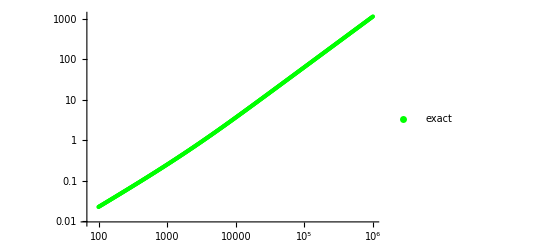

```mathematica
P0 =ListLogLogPlot[{Exp[#[[1]]], Exp[#[[1]]-#[[2]]]}&/@edectab[[500;;]],
PlotLegends->{"exact"}, PlotStyle->{Green}]
```

```mathematica
|
```

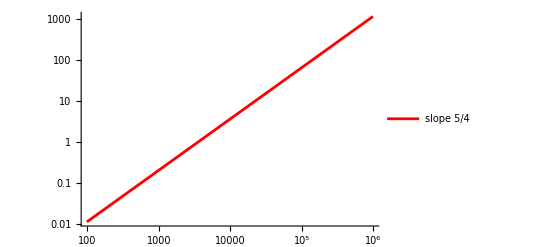

```mathematica
P1 =Block[{ x0, y0, x1, a},
a = edectab[[500]][[1]];
{x0,y0} = edectab[[-200]];
x1 = edectab[[-1]][[1]];
LogLogPlot[Exp[x0-y0] (x/Exp[x0])^(5/4),{x,Exp[a],Exp[x1]}, 
PlotLegends->{"slope 5/4"}, PlotStyle->{Red, Tiny}]
]
```

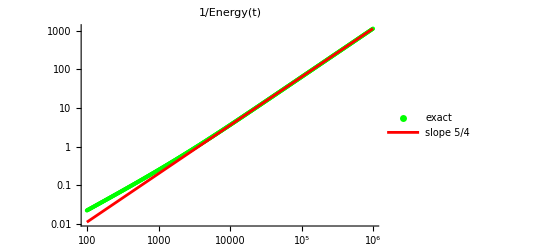

```mathematica
Show[{P0, P1}, PlotRange->All,PlotLabel->"1/Energy(t)"]
```

```mathematica
EDis[1]
```

4499.65

```mathematica
EDec[1]
```

4498.65

```mathematica
ne[t_] :=  EDis[t]/EDec[t]/t;
```

```mathematica
netable[k0_, k1_, M_] :=  
ParallelTable[Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{Log[k^2], ne[k^2]}]
,{n,0,M}];
```

```mathematica
ntab = netable[0.1, 1000,1000];
```

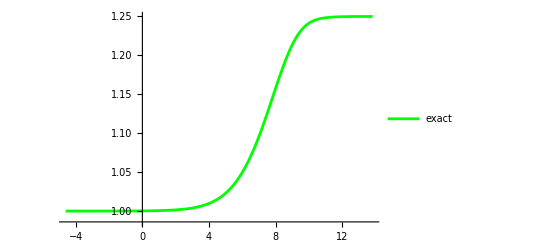

```mathematica
Pe1 =ListLinePlot[ntab, PlotStyle->Green, PlotLegends->{"exact"}]
```

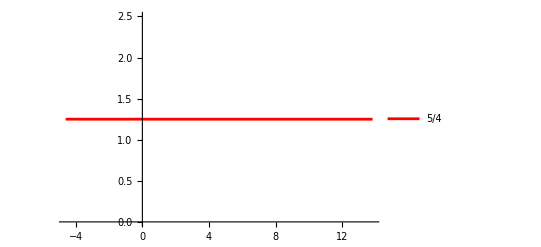

```mathematica
Pe2 = Plot[5/4,{x,2 Log[0.1], 2 Log[1000]}, PlotStyle->Red, PlotLegends->{"5/4"}]
```

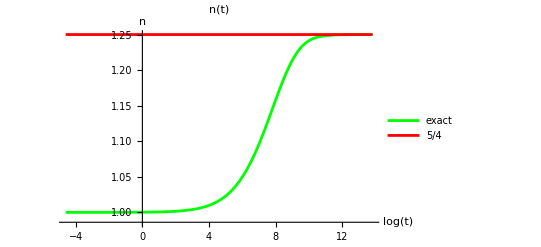

```mathematica
Show[{Pe1, Pe2}, PlotLabel->"n(t)", AxesLabel->{Log[t], n}]
```

```mathematica
(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]q(q+1))
```

```mathematica
FunctionPoles[(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]q(q+1)),p]//TableForm
```

-17/2 | 1
-13/2 | 1
-7/2 | 1
ConditionalExpression[1/2 (-17-4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1+2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/2 (-17+2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

```mathematica
Diss =FullSimplify[4 Pi ν/t^2 Integrate[κ^(p+2),{κ,k Sqrt[ ν t],Infinity}, GenerateConditions->False],{t >0, ν >0,p >0}]
```

-(4 k^4 π ν^3 (k √(t ν))^(-1+p))/(3+p)

```mathematica
Edec = Integrate[Diss,{t,t0, Infinity},GenerateConditions->False]
```

(8 k^3 π (1/t0)^(-1/2-p/2) (k √ν)^p ν^(5/2))/(3+4 p+p^2)

```mathematica
FullSimplify[Edec/.{p->2 q -1, t0->1}]
```

(2 k^2 π (k √ν)^(2 q) ν^2)/(q+q^2)

```mathematica
FullSimplify[((Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]q(q+1)))/.p-> 2 q -1]
```

-(2 Gamma[-2 q] Zeta[13/2+2 q])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q])

```mathematica
FunctionPoles[-(2 Gamma[-2 q] Zeta[13/2+2 q])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]),q]//TableForm
```

-15/4 | 1
-11/4 | 1
-5/4 | 1
-1 | 1
ConditionalExpression[1/4 (-15-4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/2 (1+2 C[1]), C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/4 (-15+2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

```mathematica
pts1 =  FunctionPoles[{-(2 Gamma[-2 q] Zeta[13/2+2 q])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]),{ Abs[q] < 40}},q]
```

{{-159/4,1},{-155/4,1},{-151/4,1},{-147/4,1},{-143/4,1},{-139/4,1},{-135/4,1},{-131/4,1},{-127/4,1},{-123/4,1},{-119/4,1},{-115/4,1},{-111/4,1},{-107/4,1},{-103/4,1},{-99/4,1},{-95/4,1},{-91/4,1},{-87/4,1},{-83/4,1},{-79/4,1},{-75/4,1},{-71/4,1},{-67/4,1},{-63/4,1},{-59/4,1},{-55/4,1},{-51/4,1},{-47/4,1},{-43/4,1},{-39/4,1},{-35/4,1},{-31/4,1},{-27/4,1},{-23/4,1},{-19/4,1},{-15/4,1},{-11/4,1},{-5/4,1},{-1,1},{0,1},{1/2,1},{1,1},{3/2,1},{2,1},{5/2,1},{3,1},{7/2,1},{4,1},{9/2,1},{5,1},{11/2,1},{6,1},{13/2,1},{7,1},{15/2,1},{8,1},{17/2,1},{9,1},{19/2,1},{10,1},{21/2,1},{11,1},{23/2,1},{12,1},{25/2,1},{13,1},{27/2,1},{14,1},{29/2,1},{15,1},{31/2,1},{16,1},{33/2,1},{17,1},{35/2,1},{18,1},{37/2,1},{19,1},{39/2,1},{20,1},{41/2,1},{21,1},{43/2,1},{22,1},{45/2,1},{23,1},{47/2,1},{24,1},{49/2,1},{25,1},{51/2,1},{26,1},{53/2,1},{27,1},{55/2,1},{28,1},{57/2,1},{29,1},{59/2,1},{30,1},{61/2,1},{31,1},{63/2,1},{32,1},{65/2,1},{33,1},{67/2,1},{34,1},{69/2,1},{35,1},{71/2,1},{36,1},{73/2,1},{37,1},{75/2,1},{38,1},{77/2,1},{39,1},{79/2,1},{1/4 (-15+2 ZetaZero[-21]),1},{1/4 (-15+2 ZetaZero[-20]),1},{1/4 (-15+2 ZetaZero[-19]),1},{1/4 (-15+2 ZetaZero[-18]),1},{1/4 (-15+2 ZetaZero[-17]),1},{1/4 (-15+2 ZetaZero[-16]),1},{1/4 (-15+2 ZetaZero[-15]),1},{1/4 (-15+2 ZetaZero[-14]),1},{1/4 (-15+2 ZetaZero[-13]),1},{1/4 (-15+2 ZetaZero[-12]),1},{1/4 (-15+2 ZetaZero[-11]),1},{1/4 (-15+2 ZetaZero[-10]),1},{1/4 (-15+2 ZetaZero[-9]),1},{1/4 (-15+2 ZetaZero[-8]),1},{1/4 (-15+2 ZetaZero[-7]),1},{1/4 (-15+2 ZetaZero[-6]),1},{1/4 (-15+2 ZetaZero[-5]),1},{1/4 (-15+2 ZetaZero[-4]),1},{1/4 (-15+2 ZetaZero[-3]),1},{1/4 (-15+2 ZetaZero[-2]),1},{1/4 (-15+2 ZetaZero[-1]),1},{1/4 (-15+2 ZetaZero[1]),1},{1/4 (-15+2 ZetaZero[2]),1},{1/4 (-15+2 ZetaZero[3]),1},{1/4 (-15+2 ZetaZero[4]),1},{1/4 (-15+2 ZetaZero[5]),1},{1/4 (-15+2 ZetaZero[6]),1},{1/4 (-15+2 ZetaZero[7]),1},{1/4 (-15+2 ZetaZero[8]),1},{1/4 (-15+2 ZetaZero[9]),1},{1/4 (-15+2 ZetaZero[10]),1},{1/4 (-15+2 ZetaZero[11]),1},{1/4 (-15+2 ZetaZero[12]),1},{1/4 (-15+2 ZetaZero[13]),1},{1/4 (-15+2 ZetaZero[14]),1},{1/4 (-15+2 ZetaZero[15]),1},{1/4 (-15+2 ZetaZero[16]),1},{1/4 (-15+2 ZetaZero[17]),1},{1/4 (-15+2 ZetaZero[18]),1},{1/4 (-15+2 ZetaZero[19]),1},{1/4 (-15+2 ZetaZero[20]),1},{1/4 (-15+2 ZetaZero[21]),1}}

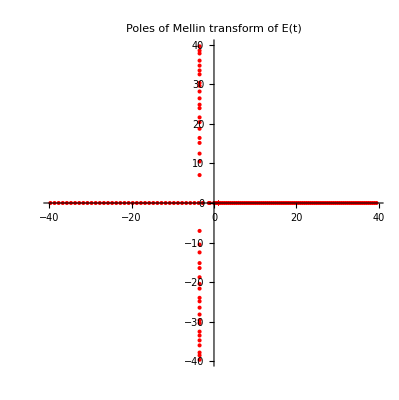

```mathematica
ComplexListPlot[pts1, PlotStyle->{Red},PlotLabel->"Poles of Mellin transform of E(t)"]
```

```mathematica
FullSimplify[Integrate[ κ ^p Sin[ κ ρ]/ ((2 Pi)^3(κ ρ)),{κ, 0, Infinity},GenerateConditions->False]/.p->-1-p,{ ρ>0, p >0}]
```

-(ρ^p Cos[(p π)/2] Gamma[-1-p])/(8 π^3)

```mathematica
FullSimplify[-(ρ^p Cos[(p π)/2] Gamma[-1-p])/(8 π^3)(((Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]))/.p->-p-1)]
```

-(ρ^p Csc[(p π)/2] Zeta[13/2-p])/(16 (75+35 p-36 p^2+4 p^3) π^2 Zeta[15/2-p])

```mathematica
Factor[(75+35 p-36 p^2+4 p^3)]
```

(1+p) (-15+2 p) (-5+2 p)

```mathematica
FunctionPoles[-(Csc[(p π)/2] Zeta[13/2-p])/(16 (1+p) (-15+2 p) (-5+2 p) π^2 Zeta[15/2-p]),p]//TableForm
```

-1 | 1
5/2 | 1
11/2 | 1
15/2 | 1
ConditionalExpression[4 C[1], C[1]∈ℤ] | 1
ConditionalExpression[1/2 (15+4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[(2 (π+2 π C[1]))/π, C[1]∈ℤ] | 1
ConditionalExpression[1/2 (15-2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

{{5/2,1},{11/2,1},{15/2,1},{19/2,1},{23/2,1},{27/2,1},{31/2,1},{35/2,1},{39/2,1},{43/2,1},{47/2,1},{51/2,1},{55/2,1},{59/2,1}}

```mathematica
pts3 = FunctionPoles[{-(Gamma[p] Gamma[1+p] Sin[(p π)/2] Zeta[13/2-p])/((-15+2 p) (-5+2 p) Zeta[15/2-p]),{6.5 <Re[p]< 7.5, Abs[Im[p]]< 30}},p]
```

{{7.+25.0109 ⅈ,1},{7.+21.022 ⅈ,1},{7.+14.1347 ⅈ,1},{7.-14.1347 ⅈ,1},{7.-21.022 ⅈ,1},{7.-25.0109 ⅈ,1}}

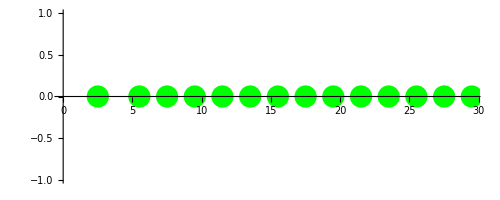

```mathematica
RP =ComplexListPlot[#[[1]]&/@pts2, PlotStyle->{Green,PointSize[0.04]}]
```

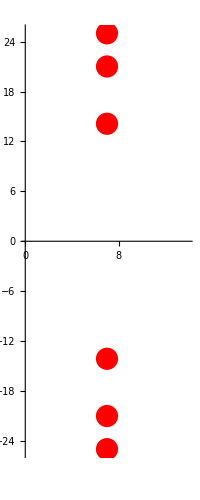

```mathematica
IP = ComplexListPlot[#[[1]]&/@pts3, PlotStyle->{Red, PointSize[0.04]}]
```

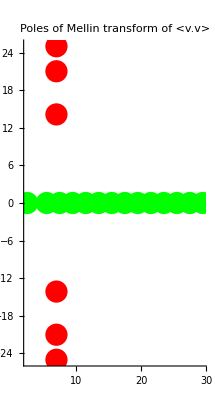

```mathematica
Show[{RP,IP},PlotLabel->"Poles of Mellin transform of <v.v>", PlotRange->All]
```

```mathematica
Series[(Gamma[p] Gamma[1+p] Sin[(p π)/2] Zeta[13/2-p])/((-15+2 p) (-5+2 p) Zeta[15/2-p]),{p,-1,0}]
```

Zeta[15/2]/(119 Zeta[17/2] (p+1)^2)+(167 Zeta[15/2] Zeta[17/2]-238 EulerGamma Zeta[15/2] Zeta[17/2]-119 Zeta[17/2] Zeta'[15/2]+119 Zeta[15/2] Zeta'[17/2])/(14161 Zeta[17/2]^2 (p+1))+1/(40443816 Zeta[17/2]^3)(520824 Zeta[15/2] Zeta[17/2]^2-953904 EulerGamma Zeta[15/2] Zeta[17/2]^2+679728 EulerGamma^2 Zeta[15/2] Zeta[17/2]^2+14161 π^2 Zeta[15/2] Zeta[17/2]^2-476952 Zeta[17/2]^2 Zeta'[15/2]+679728 EulerGamma Zeta[17/2]^2 Zeta'[15/2]+476952 Zeta[15/2] Zeta[17/2] Zeta'[17/2]-679728 EulerGamma Zeta[15/2] Zeta[17/2] Zeta'[17/2]-339864 Zeta[17/2] Zeta'[15/2] Zeta'[17/2]+339864 Zeta[15/2] Zeta'[17/2]^2+169932 Zeta[17/2]^2 Zeta''[15/2]-169932 Zeta[15/2] Zeta[17/2] Zeta''[17/2])+O[p+1]^1

```mathematica
{{5/2, 1}, {11/2, 1}, {15/2, 1}, {ConditionalExpression[2 C[1], C[1]∈Integers&&C[1]<0], 1}, {ConditionalExpression[-1+2 C[1], C[1]∈Integers&&C[1]≤0], 2}, {ConditionalExpression[1/2 (15+4 C[1]), C[1]∈Integers&&C[1]≥1], 1}, {ConditionalExpression[1/2 (15-2 ZetaZero[C[1]]), C[1]∈Integers], Indeterminate}}
```

```mathematica
ee[q_] := -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q])
```

```mathematica
Residue[ -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]), {q,-5/4}]
```

(π^(9/2) f[-7/2])/(600 Zeta[5])

```mathematica
Residue[ -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]), {q,-11/4}]/Residue[ -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]), {q,-5/4}]
```

-(10125 f[-13/2] Zeta[5])/(4 π^6 f[-7/2])

```mathematica
ABC[0.26]
```

{1.1474,0.00270802,0.0588501}

```mathematica
ff[q_]:=
Block[{ tab,OKtab, interp, delta = (Δ2 - Δ1)/1000, p = 2 q-1},
tab =(*Parallel*)Table[
Block[{A,B,C,F} ,
{A,B,C}= ABC[Δ];
(*Print[{Δ,{A,B,C}}];*)
F = 20 C^(p-1) (A C - B p);
{Δ,Log[F]}], {Δ,Δ1, Δ2, delta}];
OKtab = Select[tab,NumericQ[#[[2]]]&];
If[Length[OKtab] < 10, Return[None]];
interp = Interpolation[OKtab,InterpolationOrder->5];
NIntegrate[(1-Δ)Exp[interp[Δ]],{Δ,Δ1, Δ2}]
]
```

```mathematica
ff[-13/2]
```

1.25058×10^18

```mathematica
ff[-7/2]
```

4.09069×10^10

```mathematica
-(10125 1.2505787852221153*^18 Zeta[5])/(4 π^6 4.09068904781942*^10)
```

-8.34639×10^7

```mathematica
N[10/7]
```

1.42857

```mathematica
tdata = Flatten[ToExpression /@Import["Decaying_turbulence/k2_rega/case2.1_t.txt","Table"]];
```

```mathematica
Dimensions[tdata]
```

{2147}

```mathematica
Edata = Flatten [ToExpression /@Import["Decaying_turbulence/k2_rega/case2.1_tke.txt","Table"]];
```

```mathematica
Dimensions[Edata]
```

{2147}

```mathematica
Edata[[1]]
```

0.745992

```mathematica
tdata[[1]]
```

0.

```mathematica
tedata = Transpose[{tdata,Edata}];
```

```mathematica
tedata[[1]]
```

{0.,0.745992}

```mathematica
tedata[[-1]]
```

{125.,0.00015362}

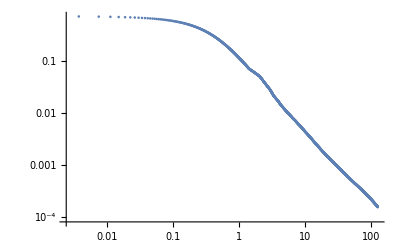

```mathematica
ListLogLogPlot[tedata]
```

```mathematica
energyDecayTab = {Exp[#[[1]]], Exp[#[[2]]-#[[1]]]}&/@edectab;
```

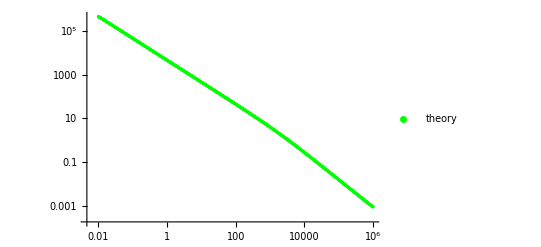

```mathematica
ListLogLogPlot[energyDecayTab,
PlotLegends->{"theory"}, PlotStyle->{Green}]
```

```mathematica
ltedata = Log[tedata[[2;;]]];
```

```mathematica
ltedata[[1]]
```

{-5.57275,-0.301589}

```mathematica
ltedata[[-1]]
```

{4.82831,-8.78103}

```mathematica
lteinterp = Interpolation[ltedata]
```

InterpolatingFunction[…]

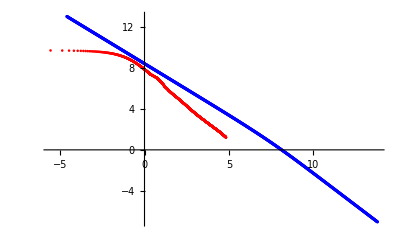

```mathematica
Show[{ ListPlot[{#[[1]], 10 +#[[2]]}& /@ltedata, PlotStyle->Red],ListLogLogPlot[energyDecayTab, PlotStyle->Blue]}, PlotRange->All]
```

```mathematica
a =.; t0 = .;
```

```mathematica
nlm =NonlinearModelFit[ltedata[[-1000;;]],a - 5/4 Log[Exp[l] + t0],{a, t0},l]
```

FittedModel[-2.70753-5/4 Log[«1»]]

```mathematica
nlm["ParameterTable"]
```

General::munfl: Exp[-4680.84] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -2.70753 | 0.000790115 | -3426.75 | 0.
t0 | -0.47367 | 0.0203582 | -23.2667 | 5.18043×10^-96

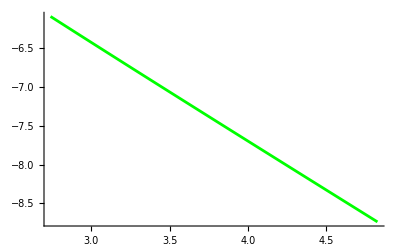

```mathematica
P2 = Plot[nlm[l],{l,ltedata[[-1000,1]], ltedata[[-1,1]]}, PlotStyle->Green]
```

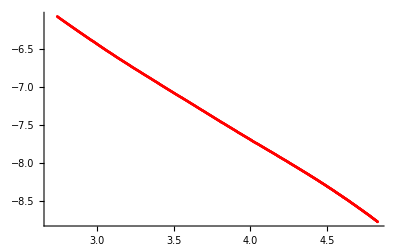

```mathematica
P1 = ListPlot[ltedata[[-1000;;]], PlotStyle->Red]
```

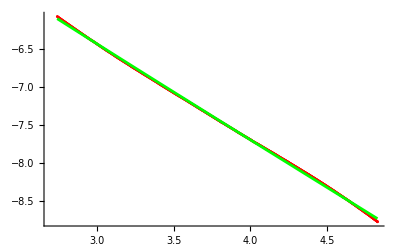

```mathematica
Show[{P1, P2}]
```

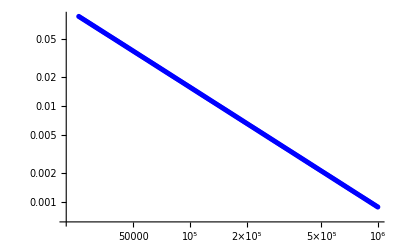

```mathematica
P3 = ListLogLogPlot[energyDecayTab[[-200;;]], PlotStyle->Blue]
```

```mathematica
p =.; t1=.;
```

```mathematica
lentab = Log[energyDecayTab];
```

```mathematica
nlm2 = NonlinearModelFit[lentab[[-200;;]],p - 5/4 l,{p},l]
```

FittedModel[10.2398-(5 l)/4]

```mathematica
nlm2["ParameterTable"]
```

General::munfl: Exp[-1848.24] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
p | 10.2398 | 0.0000681674 | 150215. | 0.

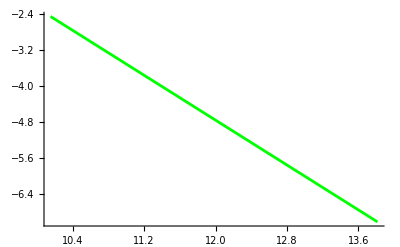

```mathematica
P4 = Plot[nlm2[l],{l,lentab[[-200,1]], lentab[[-1,1]]}, PlotStyle->Green]
```

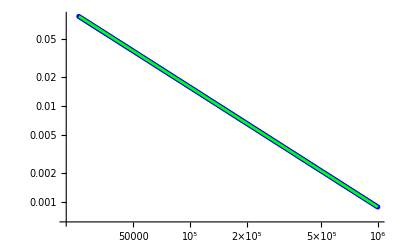

```mathematica
Show[{P3, P4}]
```

```mathematica
a=.; b= .; t0 = .;
```

```mathematica
nlm3 =NonlinearModelFit[ltedata[[-1000;;]],a + nlm2[Log[b Exp[l]+ t0]],{a,b, t0},l]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[1.81349-5/4 Log[-«19»+«19» ⅇ^l]]

```mathematica
nlm3["ParameterTable"]
```

General::munfl: Exp[-3228.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1421.4] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -8.42629 | 0.0105209 | -800.907 | 0.
b | 37.2187 | 0.292993 | 127.029 | 0.
t0 | -17.6294 | 0.619305 | -28.4664 | 6.19226×10^-131

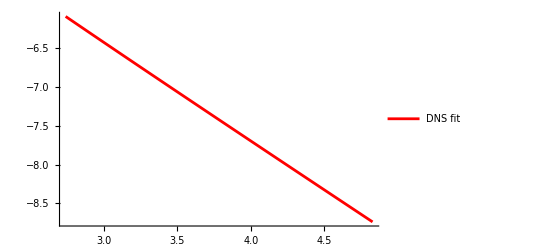

```mathematica
P5 =Plot[nlm3[l],{l, ltedata[[-1000,1]],ltedata[[-1,1]]},
 PlotStyle->Red, PlotLegends->{ "DNS fit"}]
```

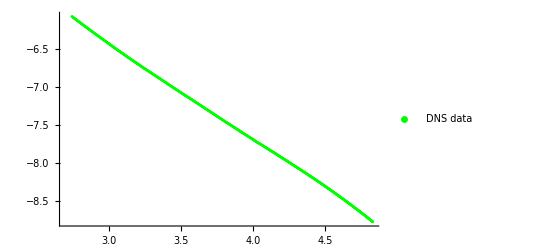

```mathematica
P6 = ListPlot[ltedata[[-1000;;]],PlotStyle->Green,PlotLegends->{ "DNS data"}]
```

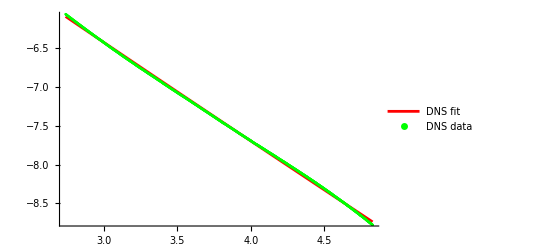

```mathematica
Show[{P5,P6}]
```

```mathematica
enInterp = Interpolation[lentab];
```

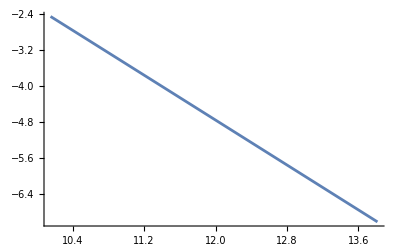

```mathematica
Plot[enInterp[l],{l, lentab[[-200,1]], lentab[[-1,1]]}]
```